Parameter alice

```mathematica
ClearAll["Global`*"]
```

```mathematica
y={0,1,1,1,0,0,1,0,0,1,0,1,1,1,1,1,1,0,0,0,1,1,0,0,1,1,1,1,1,1,1,1,1,0,1,1,0,1,1,1};
```

```mathematica
epslist = N[Range[ -4,0,(4-(0))/40]]
```

{-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.}

```mathematica
{-4,-2,10}
```

{-4,-2,10}

```mathematica
aliceRange = N[Range[-5, 5, 0.05]]
```

{-5.,-4.95,-4.9,-4.85,-4.8,-4.75,-4.7,-4.65,-4.6,-4.55,-4.5,-4.45,-4.4,-4.35,-4.3,-4.25,-4.2,-4.15,-4.1,-4.05,-4.,-3.95,-3.9,-3.85,-3.8,-3.75,-3.7,-3.65,-3.6,-3.55,-3.5,-3.45,-3.4,-3.35,-3.3,-3.25,-3.2,-3.15,-3.1,-3.05,-3.,-2.95,-2.9,-2.85,-2.8,-2.75,-2.7,-2.65,-2.6,-2.55,-2.5,-2.45,-2.4,-2.35,-2.3,-2.25,-2.2,-2.15,-2.1,-2.05,-2.,-1.95,-1.9,-1.85,-1.8,-1.75,-1.7,-1.65,-1.6,-1.55,-1.5,-1.45,-1.4,-1.35,-1.3,-1.25,-1.2,-1.15,-1.1,-1.05,-1.,-0.95,-0.9,-0.85,-0.8,-0.75,-0.7,-0.65,-0.6,-0.55,-0.5,-0.45,-0.4,-0.35,-0.3,-0.25,-0.2,-0.15,-0.1,-0.05,0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95,2.,2.05,2.1,2.15,2.2,2.25,2.3,2.35,2.4,2.45,2.5,2.55,2.6,2.65,2.7,2.75,2.8,2.85,2.9,2.95,3.,3.05,3.1,3.15,3.2,3.25,3.3,3.35,3.4,3.45,3.5,3.55,3.6,3.65,3.7,3.75,3.8,3.85,3.9,3.95,4.,4.05,4.1,4.15,4.2,4.25,4.3,4.35,4.4,4.45,4.5,4.55,4.6,4.65,4.7,4.75,4.8,4.85,4.9,4.95,5.}

```mathematica
(*Derive alice PDF*)
pNoNorm[alice_,bob_,eps_]:=
Boole[-5<=alice<=5+eps]*Boole[-5<=bob<=5]*Exp[(Plus@@Table[Boole[Boole[Abs[alice]>Abs[bob]]==y[[i]]],{i,Length[y]}])]*(0.33*PDF[NormalDistribution[1,1],alice]+(1-0.33)*PDF[NormalDistribution[0.5,0.5],alice])*
(0.33*PDF[NormalDistribution[1,1],bob]+(1-0.33)*PDF[NormalDistribution[0.5,0.5],bob])
```

```mathematica
normConstant = NIntegrate[pNoNorm[alice,bob,0],{alice,-5 ,5},{bob,-5,5}]
```

2.66019×10^11

```mathematica
ptemp[alice_, eps_] = Integrate[pNoNorm[alice,bob,eps],{bob,-Infinity,Infinity}]
```

Piecewise[{{178773., alice==0.&&eps≥-5.}, {2.59073×10^-16 ⅇ^(26.5+alice-2. alice^2) (2.06343×10^15 ⅇ^alice+5.08157×10^14 ⅇ^(1.5 alice^2)), (alice==-5.&&eps≥-10.)||(alice==5.&&eps≥0.)||(alice>5.&&alice-1. eps≤5.)}, {4.20612×10^-32 ⅇ^(-2.5 alice^2) (1.27095×10^31 ⅇ^(12.5+2. alice+0.5 alice^2)+3.12995×10^30 ⅇ^(12.5+alice+2. alice^2)-4.25773×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.-2. alice)]+4.25773×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.-2. alice)]-1.04854×10^30 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.-2. alice)]+1.04854×10^30 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.-2. alice)]+2.09709×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (-1.+alice)]-2.09709×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (-1.+alice)]+5.16447×10^29 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (-1.+alice)]-5.16447×10^29 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (-1.+alice)]+2.09709×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+alice)]-2.09709×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+alice)]+5.16447×10^29 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.+alice)]-5.16447×10^29 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.+alice)]+4.25773×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+2. alice)]-4.25773×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+2. alice)]+1.04854×10^30 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.+2. alice)]-1.04854×10^30 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.+2. alice)]), -5.<alice<0.&&alice-1. eps≤5.}, {4.20612×10^-32 ⅇ^(-2.5 alice^2) (1.27095×10^31 ⅇ^(12.5+2. alice+0.5 alice^2)+3.12995×10^30 ⅇ^(12.5+alice+2. alice^2)+4.25773×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.-2. alice)]-4.25773×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.-2. alice)]+1.04854×10^30 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.-2. alice)]-1.04854×10^30 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.-2. alice)]-2.09709×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (-1.+alice)]+2.09709×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (-1.+alice)]-5.16447×10^29 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (-1.+alice)]+5.16447×10^29 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (-1.+alice)]-2.09709×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+alice)]+2.09709×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+alice)]-5.16447×10^29 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.+alice)]+5.16447×10^29 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.+alice)]-4.25773×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+2. alice)]+4.25773×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+2. alice)]-1.04854×10^30 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.+2. alice)]+1.04854×10^30 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.+2. alice)]), 0.<alice<5.&&alice-1. eps≤5.}, {0., True}}]

```mathematica
p[alice_]=ptemp[alice,0]/normConstant
```

3.75913×10^-12 (Piecewise[{{178773., alice==0.}, {2.59073×10^-16 ⅇ^(26.5+alice-2. alice^2) (2.06343×10^15 ⅇ^alice+5.08157×10^14 ⅇ^(1.5 alice^2)), alice==-5.||alice==5.||(alice>5.&&0.+alice≤5.)}, {4.20612×10^-32 ⅇ^(-2.5 alice^2) (1.27095×10^31 ⅇ^(12.5+2. alice+0.5 alice^2)+3.12995×10^30 ⅇ^(12.5+alice+2. alice^2)-4.25773×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.-2. alice)]+4.25773×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.-2. alice)]-1.04854×10^30 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.-2. alice)]+1.04854×10^30 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.-2. alice)]+2.09709×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (-1.+alice)]-2.09709×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (-1.+alice)]+5.16447×10^29 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (-1.+alice)]-5.16447×10^29 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (-1.+alice)]+2.09709×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+alice)]-2.09709×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+alice)]+5.16447×10^29 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.+alice)]-5.16447×10^29 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.+alice)]+4.25773×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+2. alice)]-4.25773×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+2. alice)]+1.04854×10^30 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.+2. alice)]-1.04854×10^30 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.+2. alice)]), -5.<alice<0.&&0.+alice≤5.}, {4.20612×10^-32 ⅇ^(-2.5 alice^2) (1.27095×10^31 ⅇ^(12.5+2. alice+0.5 alice^2)+3.12995×10^30 ⅇ^(12.5+alice+2. alice^2)+4.25773×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.-2. alice)]-4.25773×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.-2. alice)]+1.04854×10^30 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.-2. alice)]-1.04854×10^30 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.-2. alice)]-2.09709×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (-1.+alice)]+2.09709×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (-1.+alice)]-5.16447×10^29 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (-1.+alice)]+5.16447×10^29 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (-1.+alice)]-2.09709×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+alice)]+2.09709×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+alice)]-5.16447×10^29 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.+alice)]+5.16447×10^29 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.+alice)]-4.25773×10^30 ⅇ^(12.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+2. alice)]+4.25773×10^30 ⅇ^(26.5+2. alice+0.5 alice^2) Erf[0.707107 (1.+2. alice)]-1.04854×10^30 ⅇ^(12.5+alice+2. alice^2) Erf[0.707107 (1.+2. alice)]+1.04854×10^30 ⅇ^(26.5+2. alice+alice (-1.+2. alice)) Erf[0.707107 (1.+2. alice)]), 0.<alice<5.&&0.+alice≤5.}, {0., True}}])

```mathematica
NIntegrate[p[alice], {alice, -5, 5}]
```

0.999999

```mathematica
aliceExp = NIntegrate[p[alice]*alice, {alice, -5, 5}]
```

1.00232

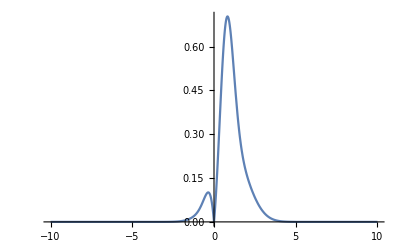

```mathematica
(*Visulize PDF*)
Plot[p[alice],{alice,-10,10},PlotRange->Full]
```

```mathematica
aliceTable = Table[p[alice], {alice, aliceRange}]
```

{4.01012×10^-9,5.40632×10^-9,7.27043×10^-9,9.75287×10^-9,1.30503×10^-8,1.74188×10^-8,2.31917×10^-8,3.08007×10^-8,4.08039×10^-8,5.39209×10^-8,7.10763×10^-8,9.34558×10^-8,1.22575×10^-7,1.60364×10^-7,2.0928×10^-7,2.72433×10^-7,3.53755×10^-7,4.58203×10^-7,5.92003×10^-7,7.62958×10^-7,9.80817×10^-7,1.25772×10^-6,1.60875×10^-6,2.05259×10^-6,2.6123×10^-6,3.31627×10^-6,4.19935×10^-6,5.30419×10^-6,6.68279×10^-6,8.39844×10^-6,0.0000105278,0.0000131637,0.0000164178,0.0000204242,0.0000253436,0.0000313678,0.0000387245,0.0000476842,0.0000585661,0.0000717462,0.0000876656,0.00010684,0.000129871,0.000157455,0.0001904,0.000229635,0.000276228,0.000331399,0.00039654,0.000473227,0.000563243,0.000668594,0.000791529,0.000934554,0.00110046,0.00129232,0.00151354,0.00176785,0.0020593,0.00239234,0.00277175,0.00320274,0.00369092,0.00424232,0.0048635,0.00556153,0.00634416,0.00721987,0.00819815,0.00928967,0.0105066,0.0118632,0.0133759,0.0150642,0.0169512,0.0190636,0.0214326,0.0240934,0.0270848,0.0304476,0.0342226,0.0384465,0.0431469,0.048336,0.054002,0.0601003,0.066543,0.0731894,0.0798362,0.0862102,0.0919643,0.0966762,0.0998526,0.100939,0.0993349,0.0944134,0.0855487,0.0721468,0.0536799,0.0297247,6.72033×10^-7,0.0355932,0.0769387,0.123679,0.175197,0.230612,0.288791,0.348384,0.40787,0.465626,0.520008,0.569442,0.612508,0.648026,0.675123,0.693275,0.702335,0.702523,0.694393,0.678786,0.656761,0.629515,0.598312,0.564403,0.52897,0.493073,0.457614,0.423325,0.390758,0.36029,0.332146,0.306415,0.283075,0.262023,0.243095,0.226089,0.210788,0.196969,0.18442,0.172944,0.162366,0.152538,0.143334,0.134653,0.126416,0.118563,0.111049,0.103846,0.0969342,0.0903009,0.083941,0.0778526,0.0720359,0.0664925,0.0612241,0.0562318,0.0515158,0.0470749,0.0429067,0.0390071,0.0353708,0.031991,0.0288598,0.0259683,0.0233067,0.0208643,0.0186302,0.0165928,0.0147407,0.0130621,0.0115452,0.0101786,0.00895114,0.00785179,0.00687008,0.00599597,0.00521989,0.00453284,0.00392633,0.00339243,0.00292377,0.00251354,0.00215545,0.00184375,0.00157317,0.00133894,0.00113674,0.000962653,0.00081319,0.000685216,0.000575938,0.000482877,0.000403842,0.000336899,0.00028035,0.000232711,0.000192684,0.000159144,0.000131113,0.00010775,0.0000883287}

```mathematica
aliceNorm = Total[aliceTable]
aliceTable = aliceTable / aliceNorm
aliceTrueCDF= Table[Function[upto,Sum[aliceTable[[i]], {i, 1,upto}]][i], {i,1, Length[aliceTable]}]
```

19.9946

{2.0056×10^-10,2.70389×10^-10,3.6362×10^-10,4.87776×10^-10,6.52689×10^-10,8.71178×10^-10,1.1599×10^-9,1.54045×10^-9,2.04075×10^-9,2.69677×10^-9,3.55478×10^-9,4.67406×10^-9,6.13039×10^-9,8.02038×10^-9,1.04668×10^-8,1.36253×10^-8,1.76925×10^-8,2.29163×10^-8,2.96082×10^-8,3.81582×10^-8,4.90541×10^-8,6.29031×10^-8,8.04595×10^-8,1.02657×10^-7,1.30651×10^-7,1.65859×10^-7,2.10025×10^-7,2.65281×10^-7,3.3423×10^-7,4.20036×10^-7,5.26535×10^-7,6.58364×10^-7,8.21112×10^-7,1.02149×10^-6,1.26753×10^-6,1.56881×10^-6,1.93675×10^-6,2.38486×10^-6,2.9291×10^-6,3.58828×10^-6,4.38447×10^-6,5.34345×10^-6,6.49529×10^-6,7.87487×10^-6,9.52255×10^-6,0.0000114848,0.0000138151,0.0000165744,0.0000198324,0.0000236677,0.0000281698,0.0000334388,0.0000395871,0.0000467404,0.0000550378,0.0000646336,0.0000756977,0.0000884163,0.000102993,0.000119649,0.000138625,0.000160181,0.000184596,0.000212174,0.000243241,0.000278152,0.000317294,0.000361091,0.000410019,0.000464609,0.000525474,0.000593321,0.000668976,0.000753416,0.000847789,0.000953438,0.00107192,0.001205,0.0013546,0.00152279,0.00171159,0.00192284,0.00215793,0.00241745,0.00270083,0.00300583,0.00332805,0.00366046,0.00399289,0.00431168,0.00459946,0.00483512,0.00499398,0.00504832,0.00496809,0.00472195,0.00427859,0.00360832,0.00268472,0.00148664,3.36107×10^-8,0.00178014,0.00384798,0.00618564,0.00876225,0.0115337,0.0144435,0.0174239,0.020399,0.0232876,0.0260075,0.0284798,0.0306337,0.0324101,0.0337653,0.0346731,0.0351263,0.0351356,0.034729,0.0339485,0.0328469,0.0314843,0.0299237,0.0282278,0.0264557,0.0246603,0.0228869,0.021172,0.0195432,0.0180194,0.0166118,0.0153249,0.0141576,0.0131047,0.012158,0.0113075,0.0105422,0.00985112,0.00922348,0.00864952,0.00812052,0.00762898,0.00716866,0.00673449,0.00632251,0.00592973,0.00555397,0.00519373,0.00484802,0.00451627,0.00419819,0.00389368,0.00360277,0.00332553,0.00306204,0.00281235,0.00257649,0.00235438,0.00214592,0.00195088,0.00176902,0.00159998,0.00144338,0.00129877,0.00116565,0.0010435,0.00093176,0.000829867,0.000737235,0.00065328,0.000577416,0.00050907,0.000447678,0.000392696,0.000343597,0.000299879,0.000261065,0.000226703,0.00019637,0.000169667,0.000146228,0.000125711,0.000107802,0.0000922124,0.0000786799,0.0000669653,0.0000568522,0.0000481457,0.0000406705,0.0000342701,0.0000288047,0.0000241504,0.0000201976,0.0000168495,0.0000140213,0.0000116387,9.63681×10^-6,7.95933×10^-6,6.55743×10^-6,5.38896×10^-6,4.41763×10^-6}

{2.0056×10^-10,4.70949×10^-10,8.34569×10^-10,1.32234×10^-9,1.97503×10^-9,2.84621×10^-9,4.00611×10^-9,5.54656×10^-9,7.58731×10^-9,1.02841×10^-8,1.38389×10^-8,1.85129×10^-8,2.46433×10^-8,3.26637×10^-8,4.31305×10^-8,5.67558×10^-8,7.44484×10^-8,9.73647×10^-8,1.26973×10^-7,1.65131×10^-7,2.14185×10^-7,2.77088×10^-7,3.57548×10^-7,4.60205×10^-7,5.90856×10^-7,7.56714×10^-7,9.66739×10^-7,1.23202×10^-6,1.56625×10^-6,1.98629×10^-6,2.51282×10^-6,3.17118×10^-6,3.9923×10^-6,5.01378×10^-6,6.28131×10^-6,7.85012×10^-6,9.78687×10^-6,0.0000121717,0.0000151008,0.0000186891,0.0000230736,0.000028417,0.0000349123,0.0000427872,0.0000523097,0.0000637946,0.0000776097,0.0000941841,0.000114016,0.000137684,0.000165854,0.000199293,0.00023888,0.00028562,0.000340658,0.000405292,0.000480989,0.000569406,0.000672399,0.000792048,0.000930673,0.00109085,0.00127545,0.00148762,0.00173086,0.00200902,0.00232631,0.0026874,0.00309742,0.00356203,0.0040875,0.00468082,0.0053498,0.00610322,0.006951,0.00790444,0.00897636,0.0101814,0.011536,0.0130588,0.0147703,0.0166932,0.0188511,0.0212686,0.0239694,0.0269752,0.0303033,0.0339637,0.0379566,0.0422683,0.0468678,0.0517029,0.0566969,0.0617452,0.0667133,0.0714352,0.0757138,0.0793221,0.0820069,0.0834935,0.0834935,0.0852737,0.0891217,0.0953073,0.10407,0.115603,0.130047,0.147471,0.16787,0.191157,0.217165,0.245645,0.276278,0.308688,0.342454,0.377127,0.412253,0.447389,0.482118,0.516066,0.548913,0.580397,0.610321,0.638549,0.665004,0.689665,0.712552,0.733724,0.753267,0.771286,0.787898,0.803223,0.817381,0.830485,0.842643,0.853951,0.864493,0.874344,0.883568,0.892217,0.900338,0.907967,0.915135,0.92187,0.928192,0.934122,0.939676,0.94487,0.949718,0.954234,0.958432,0.962326,0.965929,0.969254,0.972316,0.975129,0.977705,0.980059,0.982205,0.984156,0.985925,0.987525,0.988969,0.990267,0.991433,0.992477,0.993408,0.994238,0.994975,0.995629,0.996206,0.996715,0.997163,0.997556,0.997899,0.998199,0.99846,0.998687,0.998883,0.999053,0.999199,0.999325,0.999433,0.999525,0.999603,0.99967,0.999727,0.999775,0.999816,0.99985,0.999879,0.999903,0.999924,0.99994,0.999954,0.999966,0.999976,0.999984,0.99999,0.999996,1.}

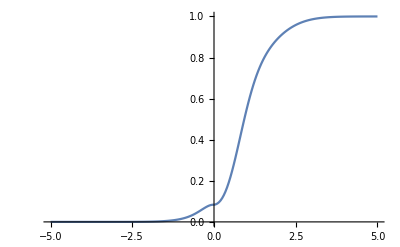

```mathematica
(*Visulize CDF*)
ListLinePlot[Transpose[{aliceRange,aliceTrueCDF}],PlotRange->{Automatic,Full}]
```

```mathematica
matrix = Table[0,{r,Length[aliceRange]},{c, Length[epslist]}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
For[i = 1, i <= Length[epslist], i++,
 eps = epslist[[i]];normEps = NIntegrate[pNoNorm[alice,bob,eps],{alice,-5,5 + eps},{bob,-5,5}];
Print["eps: ", eps, ",normEps: ", normEps];
peps[alice_]:=ptemp[alice, eps]/normEps;
Print["eps: ", eps,"p[alice=2]: ",peps[2]];
aliceTableEps = Table[peps[alice], {alice, aliceRange}];
aliceNormEps = Total[aliceTableEps];
aliceTableEps = aliceTableEps / aliceNormEps;
aliceCDFEps= Table[Function[upto,Sum[aliceTableEps[[i]], {i, 1,upto}]][i], {i,1, Length[aliceTableEps]}];
matrix[[All,i]] = aliceCDFEps;
 ]
```

eps: -4.,normEps: 1.41714×10^11

eps: -4.p[alice=2]: 0.

eps: -3.9,normEps: 1.58443×10^11

eps: -3.9p[alice=2]: 0.

eps: -3.8,normEps: 1.7345×10^11

eps: -3.8p[alice=2]: 0.

eps: -3.7,normEps: 1.86569×10^11

eps: -3.7p[alice=2]: 0.

eps: -3.6,normEps: 1.97838×10^11

eps: -3.6p[alice=2]: 0.

eps: -3.5,normEps: 2.07432×10^11

eps: -3.5p[alice=2]: 0.

eps: -3.4,normEps: 2.15594×10^11

eps: -3.4p[alice=2]: 0.

eps: -3.3,normEps: 2.22574×10^11

eps: -3.3p[alice=2]: 0.

eps: -3.2,normEps: 2.28596×10^11

eps: -3.2p[alice=2]: 0.

eps: -3.1,normEps: 2.33841×10^11

eps: -3.1p[alice=2]: 0.

eps: -3.,normEps: 2.38446×10^11

eps: -3.p[alice=2]: 0.181142

eps: -2.9,normEps: 2.42506×10^11

eps: -2.9p[alice=2]: 0.178109

eps: -2.8,normEps: 2.4609×10^11

eps: -2.8p[alice=2]: 0.175515

eps: -2.7,normEps: 2.49246×10^11

eps: -2.7p[alice=2]: 0.173293

eps: -2.6,normEps: 2.5201×10^11

eps: -2.6p[alice=2]: 0.171392

eps: -2.5,normEps: 2.54413×10^11

eps: -2.5p[alice=2]: 0.169773

eps: -2.4,normEps: 2.56485×10^11

eps: -2.4p[alice=2]: 0.168402

eps: -2.3,normEps: 2.58255×10^11

eps: -2.3p[alice=2]: 0.167247

eps: -2.2,normEps: 2.59753×10^11

eps: -2.2p[alice=2]: 0.166283

eps: -2.1,normEps: 2.61006×10^11

eps: -2.1p[alice=2]: 0.165485

eps: -2.,normEps: 2.62045×10^11

eps: -2.p[alice=2]: 0.164829

eps: -1.9,normEps: 2.62897×10^11

eps: -1.9p[alice=2]: 0.164295

eps: -1.8,normEps: 2.63589×10^11

eps: -1.8p[alice=2]: 0.163863

eps: -1.7,normEps: 2.64145×10^11

eps: -1.7p[alice=2]: 0.163518

eps: -1.6,normEps: 2.64587×10^11

eps: -1.6p[alice=2]: 0.163245

eps: -1.5,normEps: 2.64935×10^11

eps: -1.5p[alice=2]: 0.163031

eps: -1.4,normEps: 2.65207×10^11

eps: -1.4p[alice=2]: 0.162864

eps: -1.3,normEps: 2.65416×10^11

eps: -1.3p[alice=2]: 0.162735

eps: -1.2,normEps: 2.65576×10^11

eps: -1.2p[alice=2]: 0.162637

eps: -1.1,normEps: 2.65697×10^11

eps: -1.1p[alice=2]: 0.162563

eps: -1.,normEps: 2.65787×10^11

eps: -1.p[alice=2]: 0.162508

eps: -0.9,normEps: 2.65854×10^11

eps: -0.9p[alice=2]: 0.162467

eps: -0.8,normEps: 2.65904×10^11

eps: -0.8p[alice=2]: 0.162437

eps: -0.7,normEps: 2.65939×10^11

eps: -0.7p[alice=2]: 0.162415

eps: -0.6,normEps: 2.65965×10^11

eps: -0.6p[alice=2]: 0.162399

eps: -0.5,normEps: 2.65983×10^11

eps: -0.5p[alice=2]: 0.162388

eps: -0.4,normEps: 2.65996×10^11

eps: -0.4p[alice=2]: 0.16238

eps: -0.3,normEps: 2.66005×10^11

eps: -0.3p[alice=2]: 0.162375

eps: -0.2,normEps: 2.66012×10^11

eps: -0.2p[alice=2]: 0.162371

eps: -0.1,normEps: 2.66016×10^11

eps: -0.1p[alice=2]: 0.162368

eps: 0.,normEps: 2.66019×10^11

eps: 0.p[alice=2]: 0.162366

```mathematica
MatrixForm[matrix]
```

(3.65377×10^-10 | 3.28614×10^-10 | 3.01592×10^-10 | 2.81468×10^-10 | 2.66254×10^-10 | 2.54551×10^-10 | 2.45369×10^-10 | 2.38013×10^-10 | 2.31997×10^-10 | 2.26989×10^-10 | 2.22761×10^-10 | 2.19159×10^-10 | 2.16076×10^-10 | 2.13435×10^-10 | 2.11179×10^-10 | 2.09259×10^-10 | 2.07635×10^-10 | 2.06271×10^-10 | 2.05134×10^-10 | 2.04194×10^-10 | 2.03423×10^-10 | 2.02797×10^-10 | 2.02293×10^-10 | 2.01891×10^-10 | 2.01573×10^-10 | 2.01324×10^-10 | 2.01131×10^-10 | 2.00982×10^-10 | 2.0087×10^-10 | 2.00784×10^-10 | 2.00721×10^-10 | 2.00674×10^-10 | 2.0064×10^-10 | 2.00615×10^-10 | 2.00597×10^-10 | 2.00584×10^-10 | 2.00576×10^-10 | 2.00569×10^-10 | 2.00565×10^-10 | 2.00562×10^-10 | 2.0056×10^-10
8.57967×10^-10 | 7.71642×10^-10 | 7.0819×10^-10 | 6.60934×10^-10 | 6.25209×10^-10 | 5.97729×10^-10 | 5.76169×10^-10 | 5.58895×10^-10 | 5.44769×10^-10 | 5.33009×10^-10 | 5.23081×10^-10 | 5.14623×10^-10 | 5.07383×10^-10 | 5.01183×10^-10 | 4.95883×10^-10 | 4.91375×10^-10 | 4.87561×10^-10 | 4.84358×10^-10 | 4.81689×10^-10 | 4.79482×10^-10 | 4.77672×10^-10 | 4.76202×10^-10 | 4.75019×10^-10 | 4.74074×10^-10 | 4.73328×10^-10 | 4.72743×10^-10 | 4.72289×10^-10 | 4.71941×10^-10 | 4.71676×10^-10 | 4.71476×10^-10 | 4.71327×10^-10 | 4.71217×10^-10 | 4.71136×10^-10 | 4.71078×10^-10 | 4.71036×10^-10 | 4.71006×10^-10 | 4.70985×10^-10 | 4.70971×10^-10 | 4.70961×10^-10 | 4.70954×10^-10 | 4.70949×10^-10
1.5204×10^-9 | 1.36743×10^-9 | 1.25498×10^-9 | 1.17124×10^-9 | 1.10793×10^-9 | 1.05924×10^-9 | 1.02103×10^-9 | 9.90418×10^-10 | 9.65386×10^-10 | 9.44545×10^-10 | 9.26951×10^-10 | 9.11963×10^-10 | 8.99134×10^-10 | 8.88146×10^-10 | 8.78755×10^-10 | 8.70765×10^-10 | 8.64007×10^-10 | 8.58331×10^-10 | 8.536×10^-10 | 8.49689×10^-10 | 8.46483×10^-10 | 8.43878×10^-10 | 8.41781×10^-10 | 8.40107×10^-10 | 8.38784×10^-10 | 8.37748×10^-10 | 8.36944×10^-10 | 8.36326×10^-10 | 8.35856×10^-10 | 8.35502×10^-10 | 8.35238×10^-10 | 8.35043×10^-10 | 8.349×10^-10 | 8.34797×10^-10 | 8.34723×10^-10 | 8.3467×10^-10 | 8.34633×10^-10 | 8.34607×10^-10 | 8.3459×10^-10 | 8.34577×10^-10 | 8.34569×10^-10
2.40902×10^-9 | 2.16664×10^-9 | 1.98848×10^-9 | 1.85579×10^-9 | 1.75548×10^-9 | 1.67832×10^-9 | 1.61778×10^-9 | 1.56928×10^-9 | 1.52962×10^-9 | 1.4966×10^-9 | 1.46872×10^-9 | 1.44497×10^-9 | 1.42465×10^-9 | 1.40723×10^-9 | 1.39236×10^-9 | 1.3797×10^-9 | 1.36899×10^-9 | 1.35999×10^-9 | 1.3525×10^-9 | 1.3463×10^-9 | 1.34122×10^-9 | 1.33709×10^-9 | 1.33377×10^-9 | 1.33112×10^-9 | 1.32902×10^-9 | 1.32738×10^-9 | 1.32611×10^-9 | 1.32513×10^-9 | 1.32438×10^-9 | 1.32382×10^-9 | 1.3234×10^-9 | 1.3231×10^-9 | 1.32287×10^-9 | 1.32271×10^-9 | 1.32259×10^-9 | 1.3225×10^-9 | 1.32245×10^-9 | 1.32241×10^-9 | 1.32238×10^-9 | 1.32236×10^-9 | 1.32234×10^-9
3.59808×10^-9 | 3.23606×10^-9 | 2.96996×10^-9 | 2.77178×10^-9 | 2.62196×10^-9 | 2.50671×10^-9 | 2.4163×10^-9 | 2.34386×10^-9 | 2.28462×10^-9 | 2.23529×10^-9 | 2.19366×10^-9 | 2.15819×10^-9 | 2.12783×10^-9 | 2.10182×10^-9 | 2.0796×10^-9 | 2.06069×10^-9 | 2.0447×10^-9 | 2.03127×10^-9 | 2.02007×10^-9 | 2.01082×10^-9 | 2.00323×10^-9 | 1.99706×10^-9 | 1.9921×10^-9 | 1.98814×10^-9 | 1.98501×10^-9 | 1.98256×10^-9 | 1.98065×10^-9 | 1.97919×10^-9 | 1.97808×10^-9 | 1.97724×10^-9 | 1.97662×10^-9 | 1.97616×10^-9 | 1.97582×10^-9 | 1.97557×10^-9 | 1.9754×10^-9 | 1.97527×10^-9 | 1.97519×10^-9 | 1.97512×10^-9 | 1.97508×10^-9 | 1.97505×10^-9 | 1.97503×10^-9
5.18518×10^-9 | 4.66347×10^-9 | 4.27999×10^-9 | 3.99439×10^-9 | 3.77849×10^-9 | 3.61241×10^-9 | 3.48211×10^-9 | 3.37772×10^-9 | 3.29235×10^-9 | 3.22127×10^-9 | 3.16127×10^-9 | 3.11015×10^-9 | 3.0664×10^-9 | 3.02893×10^-9 | 2.9969×10^-9 | 2.96965×10^-9 | 2.94661×10^-9 | 2.92725×10^-9 | 2.91111×10^-9 | 2.89778×10^-9 | 2.88684×10^-9 | 2.87796×10^-9 | 2.87081×10^-9 | 2.8651×10^-9 | 2.86058×10^-9 | 2.85705×10^-9 | 2.85431×10^-9 | 2.8522×10^-9 | 2.8506×10^-9 | 2.84939×10^-9 | 2.84849×10^-9 | 2.84783×10^-9 | 2.84734×10^-9 | 2.84699×10^-9 | 2.84674×10^-9 | 2.84656×10^-9 | 2.84643×10^-9 | 2.84634×10^-9 | 2.84628×10^-9 | 2.84624×10^-9 | 2.84621×10^-9
7.29826×10^-9 | 6.56394×10^-9 | 6.02419×10^-9 | 5.62221×10^-9 | 5.31832×10^-9 | 5.08456×10^-9 | 4.90116×10^-9 | 4.75422×10^-9 | 4.63406×10^-9 | 4.53402×10^-9 | 4.44957×10^-9 | 4.37762×10^-9 | 4.31604×10^-9 | 4.26329×10^-9 | 4.21821×10^-9 | 4.17986×10^-9 | 4.14742×10^-9 | 4.12017×10^-9 | 4.09746×10^-9 | 4.07869×10^-9 | 4.0633×10^-9 | 4.0508×10^-9 | 4.04073×10^-9 | 4.03269×10^-9 | 4.02634×10^-9 | 4.02137×10^-9 | 4.01751×10^-9 | 4.01455×10^-9 | 4.01229×10^-9 | 4.01059×10^-9 | 4.00932×10^-9 | 4.00839×10^-9 | 4.0077×10^-9 | 4.0072×10^-9 | 4.00685×10^-9 | 4.0066×10^-9 | 4.00642×10^-9 | 4.00629×10^-9 | 4.00621×10^-9 | 4.00615×10^-9 | 4.00611×10^-9
1.01046×10^-8 | 9.08795×10^-9 | 8.34064×10^-9 | 7.78409×10^-9 | 7.36335×10^-9 | 7.0397×10^-9 | 6.78578×10^-9 | 6.58234×10^-9 | 6.41597×10^-9 | 6.27746×10^-9 | 6.16054×10^-9 | 6.06092×10^-9 | 5.97566×10^-9 | 5.90264×10^-9 | 5.84022×10^-9 | 5.78712×10^-9 | 5.74221×10^-9 | 5.70449×10^-9 | 5.67305×10^-9 | 5.64705×10^-9 | 5.62575×10^-9 | 5.60843×10^-9 | 5.59449×10^-9 | 5.58337×10^-9 | 5.57457×10^-9 | 5.56769×10^-9 | 5.56235×10^-9 | 5.55824×10^-9 | 5.55512×10^-9 | 5.55277×10^-9 | 5.55101×10^-9 | 5.54971×10^-9 | 5.54877×10^-9 | 5.54808×10^-9 | 5.54759×10^-9 | 5.54724×10^-9 | 5.54699×10^-9 | 5.54682×10^-9 | 5.5467×10^-9 | 5.54662×10^-9 | 5.54656×10^-9
1.38224×10^-8 | 1.24317×10^-8 | 1.14094×10^-8 | 1.06481×10^-8 | 1.00725×10^-8 | 9.62982×10^-9 | 9.28248×10^-9 | 9.00418×10^-9 | 8.77661×10^-9 | 8.58713×10^-9 | 8.42719×10^-9 | 8.29092×10^-9 | 8.17429×10^-9 | 8.07439×10^-9 | 7.98902×10^-9 | 7.91638×10^-9 | 7.85494×10^-9 | 7.80334×10^-9 | 7.76033×10^-9 | 7.72477×10^-9 | 7.69563×10^-9 | 7.67195×10^-9 | 7.65288×10^-9 | 7.63766×10^-9 | 7.62563×10^-9 | 7.61621×10^-9 | 7.6089×10^-9 | 7.60329×10^-9 | 7.59902×10^-9 | 7.5958×10^-9 | 7.5934×10^-9 | 7.59162×10^-9 | 7.59032×10^-9 | 7.58938×10^-9 | 7.58871×10^-9 | 7.58823×10^-9 | 7.58789×10^-9 | 7.58766×10^-9 | 7.5875×10^-9 | 7.58739×10^-9 | 7.58731×10^-9
1.87354×10^-8 | 1.68503×10^-8 | 1.54647×10^-8 | 1.44328×10^-8 | 1.36526×10^-8 | 1.30526×10^-8 | 1.25818×10^-8 | 1.22046×10^-8 | 1.18961×10^-8 | 1.16393×10^-8 | 1.14225×10^-8 | 1.12378×10^-8 | 1.10797×10^-8 | 1.09443×10^-8 | 1.08286×10^-8 | 1.07301×10^-8 | 1.06468×10^-8 | 1.05769×10^-8 | 1.05186×10^-8 | 1.04704×10^-8 | 1.04309×10^-8 | 1.03988×10^-8 | 1.0373×10^-8 | 1.03523×10^-8 | 1.0336×10^-8 | 1.03233×10^-8 | 1.03133×10^-8 | 1.03057×10^-8 | 1.02999×10^-8 | 1.02956×10^-8 | 1.02923×10^-8 | 1.02899×10^-8 | 1.02882×10^-8 | 1.02869×10^-8 | 1.0286×10^-8 | 1.02853×10^-8 | 1.02849×10^-8 | 1.02846×10^-8 | 1.02843×10^-8 | 1.02842×10^-8 | 1.02841×10^-8
2.52114×10^-8 | 2.26747×10^-8 | 2.08102×10^-8 | 1.94216×10^-8 | 1.83718×10^-8 | 1.75643×10^-8 | 1.69308×10^-8 | 1.64232×10^-8 | 1.60081×10^-8 | 1.56625×10^-8 | 1.53708×10^-8 | 1.51222×10^-8 | 1.49095×10^-8 | 1.47273×10^-8 | 1.45716×10^-8 | 1.44391×10^-8 | 1.4327×10^-8 | 1.42329×10^-8 | 1.41544×10^-8 | 1.40896×10^-8 | 1.40364×10^-8 | 1.39932×10^-8 | 1.39584×10^-8 | 1.39307×10^-8 | 1.39088×10^-8 | 1.38916×10^-8 | 1.38782×10^-8 | 1.3868×10^-8 | 1.38602×10^-8 | 1.38543×10^-8 | 1.385×10^-8 | 1.38467×10^-8 | 1.38444×10^-8 | 1.38426×10^-8 | 1.38414×10^-8 | 1.38405×10^-8 | 1.38399×10^-8 | 1.38395×10^-8 | 1.38392×10^-8 | 1.3839×10^-8 | 1.38389×10^-8
3.37265×10^-8 | 3.03331×10^-8 | 2.78388×10^-8 | 2.59812×10^-8 | 2.45768×10^-8 | 2.34966×10^-8 | 2.26491×10^-8 | 2.19701×10^-8 | 2.14148×10^-8 | 2.09525×10^-8 | 2.05622×10^-8 | 2.02297×10^-8 | 1.99451×10^-8 | 1.97014×10^-8 | 1.94931×10^-8 | 1.93158×10^-8 | 1.91659×10^-8 | 1.904×10^-8 | 1.89351×10^-8 | 1.88483×10^-8 | 1.87772×10^-8 | 1.87194×10^-8 | 1.86729×10^-8 | 1.86358×10^-8 | 1.86064×10^-8 | 1.85834×10^-8 | 1.85656×10^-8 | 1.85519×10^-8 | 1.85415×10^-8 | 1.85336×10^-8 | 1.85278×10^-8 | 1.85234×10^-8 | 1.85203×10^-8 | 1.8518×10^-8 | 1.85163×10^-8 | 1.85152×10^-8 | 1.85143×10^-8 | 1.85138×10^-8 | 1.85134×10^-8 | 1.85131×10^-8 | 1.85129×10^-8
4.48947×10^-8 | 4.03776×10^-8 | 3.70574×10^-8 | 3.45846×10^-8 | 3.27153×10^-8 | 3.12773×10^-8 | 3.01491×10^-8 | 2.92453×10^-8 | 2.85061×10^-8 | 2.78907×10^-8 | 2.73712×10^-8 | 2.69286×10^-8 | 2.65498×10^-8 | 2.62253×10^-8 | 2.5948×10^-8 | 2.57121×10^-8 | 2.55126×10^-8 | 2.5345×10^-8 | 2.52053×10^-8 | 2.50898×10^-8 | 2.49951×10^-8 | 2.49182×10^-8 | 2.48563×10^-8 | 2.48068×10^-8 | 2.47678×10^-8 | 2.47372×10^-8 | 2.47134×10^-8 | 2.46952×10^-8 | 2.46813×10^-8 | 2.46709×10^-8 | 2.46631×10^-8 | 2.46573×10^-8 | 2.46531×10^-8 | 2.465×10^-8 | 2.46478×10^-8 | 2.46463×10^-8 | 2.46452×10^-8 | 2.46444×10^-8 | 2.46439×10^-8 | 2.46436×10^-8 | 2.46433×10^-8
5.95061×10^-8 | 5.35189×10^-8 | 4.9118×10^-8 | 4.58405×10^-8 | 4.33627×10^-8 | 4.14568×10^-8 | 3.99614×10^-8 | 3.87634×10^-8 | 3.77836×10^-8 | 3.6968×10^-8 | 3.62794×10^-8 | 3.56928×10^-8 | 3.51907×10^-8 | 3.47606×10^-8 | 3.43931×10^-8 | 3.40803×10^-8 | 3.38158×10^-8 | 3.35937×10^-8 | 3.34085×10^-8 | 3.32555×10^-8 | 3.313×10^-8 | 3.3028×10^-8 | 3.29459×10^-8 | 3.28804×10^-8 | 3.28286×10^-8 | 3.27881×10^-8 | 3.27566×10^-8 | 3.27325×10^-8 | 3.27141×10^-8 | 3.27002×10^-8 | 3.26899×10^-8 | 3.26822×10^-8 | 3.26767×10^-8 | 3.26726×10^-8 | 3.26697×10^-8 | 3.26676×10^-8 | 3.26662×10^-8 | 3.26652×10^-8 | 3.26645×10^-8 | 3.2664×10^-8 | 3.26637×10^-8
7.85744×10^-8 | 7.06686×10^-8 | 6.48575×10^-8 | 6.05297×10^-8 | 5.7258×10^-8 | 5.47412×10^-8 | 5.27668×10^-8 | 5.11848×10^-8 | 4.98911×10^-8 | 4.88141×10^-8 | 4.79048×10^-8 | 4.71302×10^-8 | 4.64672×10^-8 | 4.58993×10^-8 | 4.5414×10^-8 | 4.50011×10^-8 | 4.46519×10^-8 | 4.43585×10^-8 | 4.4114×10^-8 | 4.39119×10^-8 | 4.37462×10^-8 | 4.36116×10^-8 | 4.35032×10^-8 | 4.34167×10^-8 | 4.33483×10^-8 | 4.32948×10^-8 | 4.32532×10^-8 | 4.32213×10^-8 | 4.3197×10^-8 | 4.31787×10^-8 | 4.31651×10^-8 | 4.3155×10^-8 | 4.31476×10^-8 | 4.31423×10^-8 | 4.31385×10^-8 | 4.31357×10^-8 | 4.31338×10^-8 | 4.31325×10^-8 | 4.31316×10^-8 | 4.31309×10^-8 | 4.31305×10^-8
1.03397×10^-7 | 9.29934×10^-8 | 8.53465×10^-8 | 7.96515×10^-8 | 7.53462×10^-8 | 7.20345×10^-8 | 6.94362×10^-8 | 6.73545×10^-8 | 6.56522×10^-8 | 6.42348×10^-8 | 6.30384×10^-8 | 6.20191×10^-8 | 6.11466×10^-8 | 6.03994×10^-8 | 5.97607×10^-8 | 5.92174×10^-8 | 5.87578×10^-8 | 5.83718×10^-8 | 5.80501×10^-8 | 5.77841×10^-8 | 5.75661×10^-8 | 5.73889×10^-8 | 5.72463×10^-8 | 5.71324×10^-8 | 5.70424×10^-8 | 5.6972×10^-8 | 5.69173×10^-8 | 5.68753×10^-8 | 5.68434×10^-8 | 5.68193×10^-8 | 5.68013×10^-8 | 5.67881×10^-8 | 5.67783×10^-8 | 5.67713×10^-8 | 5.67663×10^-8 | 5.67627×10^-8 | 5.67602×10^-8 | 5.67584×10^-8 | 5.67572×10^-8 | 5.67564×10^-8 | 5.67558×10^-8
1.35629×10^-7 | 1.21982×10^-7 | 1.11952×10^-7 | 1.04481×10^-7 | 9.8834×10^-8 | 9.44898×10^-8 | 9.10816×10^-8 | 8.8351×10^-8 | 8.61179×10^-8 | 8.42588×10^-8 | 8.26894×10^-8 | 8.13523×10^-8 | 8.02079×10^-8 | 7.92277×10^-8 | 7.839×10^-8 | 7.76772×10^-8 | 7.70744×10^-8 | 7.65681×10^-8 | 7.6146×10^-8 | 7.57971×10^-8 | 7.55112×10^-8 | 7.52788×10^-8 | 7.50917×10^-8 | 7.49424×10^-8 | 7.48243×10^-8 | 7.47319×10^-8 | 7.46602×10^-8 | 7.46051×10^-8 | 7.45632×10^-8 | 7.45316×10^-8 | 7.4508×10^-8 | 7.44906×10^-8 | 7.44779×10^-8 | 7.44687×10^-8 | 7.44621×10^-8 | 7.44574×10^-8 | 7.44541×10^-8 | 7.44518×10^-8 | 7.44502×10^-8 | 7.44491×10^-8 | 7.44484×10^-8
1.77377×10^-7 | 1.5953×10^-7 | 1.46412×10^-7 | 1.36642×10^-7 | 1.29257×10^-7 | 1.23575×10^-7 | 1.19118×10^-7 | 1.15547×10^-7 | 1.12626×10^-7 | 1.10195×10^-7 | 1.08142×10^-7 | 1.06394×10^-7 | 1.04897×10^-7 | 1.03615×10^-7 | 1.0252×10^-7 | 1.01587×10^-7 | 1.00799×10^-7 | 1.00137×10^-7 | 9.95849×10^-8 | 9.91287×10^-8 | 9.87547×10^-8 | 9.84508×10^-8 | 9.8206×10^-8 | 9.80108×10^-8 | 9.78564×10^-8 | 9.77355×10^-8 | 9.76417×10^-8 | 9.75697×10^-8 | 9.75149×10^-8 | 9.74736×10^-8 | 9.74428×10^-8 | 9.742×10^-8 | 9.74033×10^-8 | 9.73913×10^-8 | 9.73826×10^-8 | 9.73765×10^-8 | 9.73722×10^-8 | 9.73691×10^-8 | 9.73671×10^-8 | 9.73657×10^-8 | 9.73647×10^-8
2.31317×10^-7 | 2.08043×10^-7 | 1.90935×10^-7 | 1.78195×10^-7 | 1.68563×10^-7 | 1.61154×10^-7 | 1.55341×10^-7 | 1.50684×10^-7 | 1.46876×10^-7 | 1.43705×10^-7 | 1.41028×10^-7 | 1.38748×10^-7 | 1.36796×10^-7 | 1.35124×10^-7 | 1.33695×10^-7 | 1.3248×10^-7 | 1.31452×10^-7 | 1.30588×10^-7 | 1.29868×10^-7 | 1.29273×10^-7 | 1.28785×10^-7 | 1.28389×10^-7 | 1.2807×10^-7 | 1.27815×10^-7 | 1.27614×10^-7 | 1.27456×10^-7 | 1.27334×10^-7 | 1.2724×10^-7 | 1.27169×10^-7 | 1.27115×10^-7 | 1.27075×10^-7 | 1.27045×10^-7 | 1.27023×10^-7 | 1.27008×10^-7 | 1.26996×10^-7 | 1.26988×10^-7 | 1.26983×10^-7 | 1.26979×10^-7 | 1.26976×10^-7 | 1.26974×10^-7 | 1.26973×10^-7
3.00833×10^-7 | 2.70564×10^-7 | 2.48316×10^-7 | 2.31746×10^-7 | 2.1922×10^-7 | 2.09584×10^-7 | 2.02025×10^-7 | 1.95968×10^-7 | 1.91015×10^-7 | 1.86891×10^-7 | 1.8341×10^-7 | 1.80444×10^-7 | 1.77906×10^-7 | 1.75732×10^-7 | 1.73874×10^-7 | 1.72293×10^-7 | 1.70956×10^-7 | 1.69833×10^-7 | 1.68897×10^-7 | 1.68123×10^-7 | 1.67488×10^-7 | 1.66973×10^-7 | 1.66558×10^-7 | 1.66227×10^-7 | 1.65965×10^-7 | 1.6576×10^-7 | 1.65601×10^-7 | 1.65479×10^-7 | 1.65386×10^-7 | 1.65316×10^-7 | 1.65263×10^-7 | 1.65225×10^-7 | 1.65197×10^-7 | 1.65176×10^-7 | 1.65161×10^-7 | 1.65151×10^-7 | 1.65144×10^-7 | 1.65139×10^-7 | 1.65135×10^-7 | 1.65133×10^-7 | 1.65131×10^-7
3.90199×10^-7 | 3.50939×10^-7 | 3.22081×10^-7 | 3.00589×10^-7 | 2.84342×10^-7 | 2.71844×10^-7 | 2.62039×10^-7 | 2.54183×10^-7 | 2.47758×10^-7 | 2.4241×10^-7 | 2.37894×10^-7 | 2.34048×10^-7 | 2.30755×10^-7 | 2.27935×10^-7 | 2.25525×10^-7 | 2.23475×10^-7 | 2.2174×10^-7 | 2.20284×10^-7 | 2.19069×10^-7 | 2.18066×10^-7 | 2.17243×10^-7 | 2.16574×10^-7 | 2.16036×10^-7 | 2.15606×10^-7 | 2.15267×10^-7 | 2.15001×10^-7 | 2.14795×10^-7 | 2.14636×10^-7 | 2.14516×10^-7 | 2.14425×10^-7 | 2.14357×10^-7 | 2.14307×10^-7 | 2.1427×10^-7 | 2.14244×10^-7 | 2.14225×10^-7 | 2.14211×10^-7 | 2.14202×10^-7 | 2.14195×10^-7 | 2.1419×10^-7 | 2.14187×10^-7 | 2.14185×10^-7
5.04795×10^-7 | 4.54004×10^-7 | 4.16671×10^-7 | 3.88868×10^-7 | 3.67849×10^-7 | 3.5168×10^-7 | 3.38995×10^-7 | 3.28832×10^-7 | 3.20521×10^-7 | 3.13602×10^-7 | 3.0776×10^-7 | 3.02784×10^-7 | 2.98525×10^-7 | 2.94876×10^-7 | 2.91759×10^-7 | 2.89106×10^-7 | 2.86862×10^-7 | 2.84978×10^-7 | 2.83407×10^-7 | 2.82108×10^-7 | 2.81044×10^-7 | 2.80179×10^-7 | 2.79483×10^-7 | 2.78927×10^-7 | 2.78488×10^-7 | 2.78144×10^-7 | 2.77877×10^-7 | 2.77672×10^-7 | 2.77516×10^-7 | 2.77398×10^-7 | 2.7731×10^-7 | 2.77246×10^-7 | 2.77198×10^-7 | 2.77164×10^-7 | 2.77139×10^-7 | 2.77122×10^-7 | 2.7711×10^-7 | 2.77101×10^-7 | 2.77095×10^-7 | 2.77091×10^-7 | 2.77088×10^-7
6.51374×10^-7 | 5.85836×10^-7 | 5.37662×10^-7 | 5.01785×10^-7 | 4.74663×10^-7 | 4.538×10^-7 | 4.37431×10^-7 | 4.24317×10^-7 | 4.13592×10^-7 | 4.04664×10^-7 | 3.97126×10^-7 | 3.90705×10^-7 | 3.85209×10^-7 | 3.80501×10^-7 | 3.76478×10^-7 | 3.73055×10^-7 | 3.7016×10^-7 | 3.67728×10^-7 | 3.65701×10^-7 | 3.64025×10^-7 | 3.62652×10^-7 | 3.61536×10^-7 | 3.60637×10^-7 | 3.5992×10^-7 | 3.59353×10^-7 | 3.58909×10^-7 | 3.58565×10^-7 | 3.58301×10^-7 | 3.58099×10^-7 | 3.57948×10^-7 | 3.57834×10^-7 | 3.57751×10^-7 | 3.5769×10^-7 | 3.57645×10^-7 | 3.57614×10^-7 | 3.57591×10^-7 | 3.57575×10^-7 | 3.57564×10^-7 | 3.57556×10^-7 | 3.57551×10^-7 | 3.57548×10^-7
8.38394×10^-7 | 7.54038×10^-7 | 6.92033×10^-7 | 6.45855×10^-7 | 6.10946×10^-7 | 5.84092×10^-7 | 5.63024×10^-7 | 5.46145×10^-7 | 5.32341×10^-7 | 5.20849×10^-7 | 5.11147×10^-7 | 5.02882×10^-7 | 4.95808×10^-7 | 4.89749×10^-7 | 4.84571×10^-7 | 4.80165×10^-7 | 4.76438×10^-7 | 4.73308×10^-7 | 4.70699×10^-7 | 4.68543×10^-7 | 4.66775×10^-7 | 4.65339×10^-7 | 4.64182×10^-7 | 4.63259×10^-7 | 4.62529×10^-7 | 4.61958×10^-7 | 4.61515×10^-7 | 4.61174×10^-7 | 4.60915×10^-7 | 4.6072×10^-7 | 4.60574×10^-7 | 4.60467×10^-7 | 4.60388×10^-7 | 4.60331×10^-7 | 4.6029×10^-7 | 4.60261×10^-7 | 4.6024×10^-7 | 4.60226×10^-7 | 4.60216×10^-7 | 4.6021×10^-7 | 4.60205×10^-7
1.07641×10^-6 | 9.68107×10^-7 | 8.88499×10^-7 | 8.29211×10^-7 | 7.84391×10^-7 | 7.49914×10^-7 | 7.22865×10^-7 | 7.01193×10^-7 | 6.83471×10^-7 | 6.68716×10^-7 | 6.5626×10^-7 | 6.45649×10^-7 | 6.36566×10^-7 | 6.28787×10^-7 | 6.22138×10^-7 | 6.16482×10^-7 | 6.11697×10^-7 | 6.07679×10^-7 | 6.04329×10^-7 | 6.0156×10^-7 | 5.99291×10^-7 | 5.97446×10^-7 | 5.95961×10^-7 | 5.94776×10^-7 | 5.9384×10^-7 | 5.93106×10^-7 | 5.92537×10^-7 | 5.921×10^-7 | 5.91767×10^-7 | 5.91516×10^-7 | 5.91329×10^-7 | 5.91191×10^-7 | 5.9109×10^-7 | 5.91017×10^-7 | 5.90964×10^-7 | 5.90927×10^-7 | 5.90901×10^-7 | 5.90883×10^-7 | 5.9087×10^-7 | 5.90862×10^-7 | 5.90856×10^-7
1.37857×10^-6 | 1.23986×10^-6 | 1.13791×10^-6 | 1.06198×10^-6 | 1.00458×10^-6 | 9.60422×10^-7 | 9.2578×10^-7 | 8.98025×10^-7 | 8.75327×10^-7 | 8.56431×10^-7 | 8.40478×10^-7 | 8.26888×10^-7 | 8.15256×10^-7 | 8.05293×10^-7 | 7.96778×10^-7 | 7.89534×10^-7 | 7.83406×10^-7 | 7.7826×10^-7 | 7.7397×10^-7 | 7.70424×10^-7 | 7.67517×10^-7 | 7.65155×10^-7 | 7.63253×10^-7 | 7.61735×10^-7 | 7.60536×10^-7 | 7.59596×10^-7 | 7.58867×10^-7 | 7.58307×10^-7 | 7.57881×10^-7 | 7.5756×10^-7 | 7.57321×10^-7 | 7.57144×10^-7 | 7.57015×10^-7 | 7.56921×10^-7 | 7.56854×10^-7 | 7.56806×10^-7 | 7.56772×10^-7 | 7.56749×10^-7 | 7.56733×10^-7 | 7.56722×10^-7 | 7.56714×10^-7
1.76119×10^-6 | 1.58398×10^-6 | 1.45373×10^-6 | 1.35673×10^-6 | 1.2834×10^-6 | 1.22698×10^-6 | 1.18273×10^-6 | 1.14727×10^-6 | 1.11827×10^-6 | 1.09413×10^-6 | 1.07375×10^-6 | 1.05639×10^-6 | 1.04153×10^-6 | 1.0288×10^-6 | 1.01792×10^-6 | 1.00867×10^-6 | 1.00084×10^-6 | 9.94264×10^-7 | 9.88784×10^-7 | 9.84253×10^-7 | 9.8054×10^-7 | 9.77522×10^-7 | 9.75092×10^-7 | 9.73154×10^-7 | 9.71621×10^-7 | 9.70421×10^-7 | 9.6949×10^-7 | 9.68774×10^-7 | 9.6823×10^-7 | 9.6782×10^-7 | 9.67514×10^-7 | 9.67288×10^-7 | 9.67122×10^-7 | 9.67003×10^-7 | 9.66917×10^-7 | 9.66856×10^-7 | 9.66813×10^-7 | 9.66783×10^-7 | 9.66762×10^-7 | 9.66748×10^-7 | 9.66739×10^-7
2.24447×10^-6 | 2.01864×10^-6 | 1.85265×10^-6 | 1.72903×10^-6 | 1.63557×10^-6 | 1.56368×10^-6 | 1.50728×10^-6 | 1.46209×10^-6 | 1.42514×10^-6 | 1.39437×10^-6 | 1.3684×10^-6 | 1.34627×10^-6 | 1.32733×10^-6 | 1.31111×10^-6 | 1.29725×10^-6 | 1.28545×10^-6 | 1.27548×10^-6 | 1.2671×10^-6 | 1.26011×10^-6 | 1.25434×10^-6 | 1.24961×10^-6 | 1.24576×10^-6 | 1.24267×10^-6 | 1.2402×10^-6 | 1.23824×10^-6 | 1.23671×10^-6 | 1.23553×10^-6 | 1.23461×10^-6 | 1.23392×10^-6 | 1.2334×10^-6 | 1.23301×10^-6 | 1.23272×10^-6 | 1.23251×10^-6 | 1.23236×10^-6 | 1.23225×10^-6 | 1.23217×10^-6 | 1.23211×10^-6 | 1.23208×10^-6 | 1.23205×10^-6 | 1.23203×10^-6 | 1.23202×10^-6
2.85337×10^-6 | 2.56627×10^-6 | 2.35525×10^-6 | 2.19809×10^-6 | 2.07928×10^-6 | 1.98788×10^-6 | 1.91618×10^-6 | 1.85873×10^-6 | 1.81176×10^-6 | 1.77264×10^-6 | 1.73963×10^-6 | 1.7115×10^-6 | 1.68742×10^-6 | 1.6668×10^-6 | 1.64917×10^-6 | 1.63418×10^-6 | 1.6215×10^-6 | 1.61084×10^-6 | 1.60197×10^-6 | 1.59463×10^-6 | 1.58861×10^-6 | 1.58372×10^-6 | 1.57978×10^-6 | 1.57664×10^-6 | 1.57416×10^-6 | 1.57221×10^-6 | 1.57071×10^-6 | 1.56955×10^-6 | 1.56867×10^-6 | 1.568×10^-6 | 1.56751×10^-6 | 1.56714×10^-6 | 1.56687×10^-6 | 1.56668×10^-6 | 1.56654×10^-6 | 1.56644×10^-6 | 1.56637×10^-6 | 1.56632×10^-6 | 1.56629×10^-6 | 1.56627×10^-6 | 1.56625×10^-6
3.61858×10^-6 | 3.25449×10^-6 | 2.98688×10^-6 | 2.78757×10^-6 | 2.6369×10^-6 | 2.52099×10^-6 | 2.43006×10^-6 | 2.35721×10^-6 | 2.29763×10^-6 | 2.24803×10^-6 | 2.20616×10^-6 | 2.17048×10^-6 | 2.13995×10^-6 | 2.1138×10^-6 | 2.09145×10^-6 | 2.07243×10^-6 | 2.05635×10^-6 | 2.04284×10^-6 | 2.03158×10^-6 | 2.02227×10^-6 | 2.01464×10^-6 | 2.00844×10^-6 | 2.00345×10^-6 | 1.99947×10^-6 | 1.99632×10^-6 | 1.99385×10^-6 | 1.99194×10^-6 | 1.99047×10^-6 | 1.98935×10^-6 | 1.98851×10^-6 | 1.98788×10^-6 | 1.98741×10^-6 | 1.98707×10^-6 | 1.98683×10^-6 | 1.98665×10^-6 | 1.98653×10^-6 | 1.98644×10^-6 | 1.98638×10^-6 | 1.98633×10^-6 | 1.98631×10^-6 | 1.98629×10^-6
4.57781×10^-6 | 4.11721×10^-6 | 3.77865×10^-6 | 3.52651×10^-6 | 3.3359×10^-6 | 3.18927×10^-6 | 3.07424×10^-6 | 2.98207×10^-6 | 2.9067×10^-6 | 2.84395×10^-6 | 2.79098×10^-6 | 2.74585×10^-6 | 2.70722×10^-6 | 2.67414×10^-6 | 2.64586×10^-6 | 2.6218×10^-6 | 2.60146×10^-6 | 2.58437×10^-6 | 2.57012×10^-6 | 2.55835×10^-6 | 2.54869×10^-6 | 2.54085×10^-6 | 2.53453×10^-6 | 2.52949×10^-6 | 2.52551×10^-6 | 2.52239×10^-6 | 2.51997×10^-6 | 2.51811×10^-6 | 2.5167×10^-6 | 2.51563×10^-6 | 2.51483×10^-6 | 2.51425×10^-6 | 2.51382×10^-6 | 2.51351×10^-6 | 2.51328×10^-6 | 2.51312×10^-6 | 2.51301×10^-6 | 2.51294×10^-6 | 2.51288×10^-6 | 2.51285×10^-6 | 2.51282×10^-6
5.77721×10^-6 | 5.19593×10^-6 | 4.76867×10^-6 | 4.45046×10^-6 | 4.20991×10^-6 | 4.02487×10^-6 | 3.87969×10^-6 | 3.76338×10^-6 | 3.66826×10^-6 | 3.58907×10^-6 | 3.52222×10^-6 | 3.46526×10^-6 | 3.41652×10^-6 | 3.37476×10^-6 | 3.33908×10^-6 | 3.30872×10^-6 | 3.28304×10^-6 | 3.26147×10^-6 | 3.2435×10^-6 | 3.22864×10^-6 | 3.21646×10^-6 | 3.20656×10^-6 | 3.19859×10^-6 | 3.19223×10^-6 | 3.1872×10^-6 | 3.18326×10^-6 | 3.18021×10^-6 | 3.17786×10^-6 | 3.17608×10^-6 | 3.17473×10^-6 | 3.17373×10^-6 | 3.17299×10^-6 | 3.17244×10^-6 | 3.17205×10^-6 | 3.17177×10^-6 | 3.17157×10^-6 | 3.17143×10^-6 | 3.17133×10^-6 | 3.17126×10^-6 | 3.17122×10^-6 | 3.17118×10^-6
7.27309×10^-6 | 6.54131×10^-6 | 6.00341×10^-6 | 5.60282×10^-6 | 5.29998×10^-6 | 5.06702×10^-6 | 4.88426×10^-6 | 4.73783×10^-6 | 4.61808×10^-6 | 4.51838×10^-6 | 4.43422×10^-6 | 4.36252×10^-6 | 4.30115×10^-6 | 4.24859×10^-6 | 4.20367×10^-6 | 4.16544×10^-6 | 4.13312×10^-6 | 4.10597×10^-6 | 4.08333×10^-6 | 4.06463×10^-6 | 4.04929×10^-6 | 4.03683×10^-6 | 4.02679×10^-6 | 4.01879×10^-6 | 4.01246×10^-6 | 4.0075×10^-6 | 4.00366×10^-6 | 4.0007×10^-6 | 3.99845×10^-6 | 3.99676×10^-6 | 3.9955×10^-6 | 3.99456×10^-6 | 3.99388×10^-6 | 3.99339×10^-6 | 3.99303×10^-6 | 3.99278×10^-6 | 3.9926×10^-6 | 3.99248×10^-6 | 3.99239×10^-6 | 3.99234×10^-6 | 3.9923×10^-6
9.13402×10^-6 | 8.21499×10^-6 | 7.53947×10^-6 | 7.03638×10^-6 | 6.65605×10^-6 | 6.36349×10^-6 | 6.13397×10^-6 | 5.95007×10^-6 | 5.79968×10^-6 | 5.67448×10^-6 | 5.56878×10^-6 | 5.47874×10^-6 | 5.40166×10^-6 | 5.33565×10^-6 | 5.27924×10^-6 | 5.23123×10^-6 | 5.19064×10^-6 | 5.15654×10^-6 | 5.12811×10^-6 | 5.10462×10^-6 | 5.08536×10^-6 | 5.06971×10^-6 | 5.05711×10^-6 | 5.04705×10^-6 | 5.0391×10^-6 | 5.03288×10^-6 | 5.02805×10^-6 | 5.02434×10^-6 | 5.02152×10^-6 | 5.01939×10^-6 | 5.0178×10^-6 | 5.01663×10^-6 | 5.01577×10^-6 | 5.01515×10^-6 | 5.01471×10^-6 | 5.01439×10^-6 | 5.01417×10^-6 | 5.01401×10^-6 | 5.01391×10^-6 | 5.01383×10^-6 | 5.01378×10^-6
0.0000114432 | 0.0000102918 | 9.44551×10^-6 | 8.81523×10^-6 | 8.33876×10^-6 | 7.97224×10^-6 | 7.68468×10^-6 | 7.45429×10^-6 | 7.26589×10^-6 | 7.10903×10^-6 | 6.97661×10^-6 | 6.8638×10^-6 | 6.76725×10^-6 | 6.68455×10^-6 | 6.61387×10^-6 | 6.55373×10^-6 | 6.50287×10^-6 | 6.46015×10^-6 | 6.42454×10^-6 | 6.39511×10^-6 | 6.37098×10^-6 | 6.35137×10^-6 | 6.33559×10^-6 | 6.32299×10^-6 | 6.31303×10^-6 | 6.30523×10^-6 | 6.29918×10^-6 | 6.29453×10^-6 | 6.291×10^-6 | 6.28833×10^-6 | 6.28634×10^-6 | 6.28488×10^-6 | 6.2838×10^-6 | 6.28302×10^-6 | 6.28246×10^-6 | 6.28207×10^-6 | 6.28179×10^-6 | 6.2816×10^-6 | 6.28146×10^-6 | 6.28137×10^-6 | 6.28131×10^-6
0.0000143012 | 0.0000128623 | 0.0000118046 | 0.0000110169 | 0.0000104214 | 9.96337×10^-6 | 9.604×10^-6 | 9.31607×10^-6 | 9.08061×10^-6 | 8.88457×10^-6 | 8.71909×10^-6 | 8.5781×10^-6 | 8.45743×10^-6 | 8.35407×10^-6 | 8.26574×10^-6 | 8.19059×10^-6 | 8.12702×10^-6 | 8.07363×10^-6 | 8.02913×10^-6 | 7.99234×10^-6 | 7.96219×10^-6 | 7.93768×10^-6 | 7.91795×10^-6 | 7.90221×10^-6 | 7.88976×10^-6 | 7.88002×10^-6 | 7.87246×10^-6 | 7.86665×10^-6 | 7.86223×10^-6 | 7.8589×10^-6 | 7.85641×10^-6 | 7.85458×10^-6 | 7.85324×10^-6 | 7.85226×10^-6 | 7.85157×10^-6 | 7.85107×10^-6 | 7.85072×10^-6 | 7.85048×10^-6 | 7.85031×10^-6 | 7.8502×10^-6 | 7.85012×10^-6
0.0000178295 | 0.0000160356 | 0.000014717 | 0.000013735 | 0.0000129926 | 0.0000124215 | 0.0000119735 | 0.0000116145 | 0.0000113209 | 0.0000110765 | 0.0000108702 | 0.0000106945 | 0.000010544 | 0.0000104152 | 0.000010305 | 0.0000102113 | 0.0000101321 | 0.0000100655 | 0.00001001 | 9.96418×10^-6 | 9.92659×10^-6 | 9.89604×10^-6 | 9.87144×10^-6 | 9.85181×10^-6 | 9.83629×10^-6 | 9.82414×10^-6 | 9.81472×10^-6 | 9.80748×10^-6 | 9.80197×10^-6 | 9.79781×10^-6 | 9.79472×10^-6 | 9.79243×10^-6 | 9.79075×10^-6 | 9.78954×10^-6 | 9.78867×10^-6 | 9.78805×10^-6 | 9.78762×10^-6 | 9.78732×10^-6 | 9.78711×10^-6 | 9.78697×10^-6 | 9.78687×10^-6
0.0000221742 | 0.0000199432 | 0.0000183032 | 0.0000170819 | 0.0000161586 | 0.0000154484 | 0.0000148911 | 0.0000144447 | 0.0000140796 | 0.0000137757 | 0.0000135191 | 0.0000133005 | 0.0000131134 | 0.0000129531 | 0.0000128162 | 0.0000126996 | 0.0000126011 | 0.0000125183 | 0.0000124493 | 0.0000123922 | 0.0000123455 | 0.0000123075 | 0.0000122769 | 0.0000122525 | 0.0000122332 | 0.0000122181 | 0.0000122064 | 0.0000121974 | 0.0000121905 | 0.0000121853 | 0.0000121815 | 0.0000121786 | 0.0000121766 | 0.000012175 | 0.000012174 | 0.0000121732 | 0.0000121727 | 0.0000121723 | 0.000012172 | 0.0000121718 | 0.0000121717
0.0000275104 | 0.0000247424 | 0.0000227079 | 0.0000211926 | 0.0000200471 | 0.000019166 | 0.0000184747 | 0.0000179208 | 0.0000174678 | 0.0000170907 | 0.0000167724 | 0.0000165012 | 0.0000162691 | 0.0000160702 | 0.0000159003 | 0.0000157558 | 0.0000156335 | 0.0000155308 | 0.0000154452 | 0.0000153744 | 0.0000153164 | 0.0000152693 | 0.0000152313 | 0.000015201 | 0.0000151771 | 0.0000151583 | 0.0000151438 | 0.0000151326 | 0.0000151241 | 0.0000151177 | 0.0000151129 | 0.0000151094 | 0.0000151068 | 0.0000151049 | 0.0000151036 | 0.0000151027 | 0.000015102 | 0.0000151015 | 0.0000151012 | 0.000015101 | 0.0000151008
0.0000340475 | 0.0000306218 | 0.0000281037 | 0.0000262284 | 0.0000248107 | 0.0000237202 | 0.0000228646 | 0.0000221791 | 0.0000216186 | 0.0000211519 | 0.0000207579 | 0.0000204222 | 0.000020135 | 0.0000198889 | 0.0000196786 | 0.0000194997 | 0.0000193483 | 0.0000192212 | 0.0000191153 | 0.0000190277 | 0.0000189559 | 0.0000188976 | 0.0000188506 | 0.0000188131 | 0.0000187835 | 0.0000187603 | 0.0000187423 | 0.0000187285 | 0.0000187179 | 0.00001871 | 0.0000187041 | 0.0000186997 | 0.0000186965 | 0.0000186942 | 0.0000186925 | 0.0000186914 | 0.0000186905 | 0.00001869 | 0.0000186896 | 0.0000186893 | 0.0000186891
0.000042035 | 0.0000378056 | 0.0000346969 | 0.0000323816 | 0.0000306313 | 0.000029285 | 0.0000282287 | 0.0000273824 | 0.0000266903 | 0.0000261141 | 0.0000256277 | 0.0000252133 | 0.0000248586 | 0.0000245548 | 0.0000242952 | 0.0000240743 | 0.0000238875 | 0.0000237305 | 0.0000235997 | 0.0000234916 | 0.000023403 | 0.0000233309 | 0.000023273 | 0.0000232267 | 0.0000231901 | 0.0000231614 | 0.0000231392 | 0.0000231222 | 0.0000231092 | 0.0000230994 | 0.0000230921 | 0.0000230867 | 0.0000230827 | 0.0000230799 | 0.0000230778 | 0.0000230764 | 0.0000230753 | 0.0000230746 | 0.0000230741 | 0.0000230738 | 0.0000230736
0.0000517696 | 0.0000465608 | 0.0000427321 | 0.0000398807 | 0.000037725 | 0.0000360669 | 0.000034766 | 0.0000337237 | 0.0000328713 | 0.0000321617 | 0.0000315626 | 0.0000310523 | 0.0000306155 | 0.0000302413 | 0.0000299215 | 0.0000296495 | 0.0000294194 | 0.0000292261 | 0.000029065 | 0.0000289319 | 0.0000288227 | 0.000028734 | 0.0000286626 | 0.0000286056 | 0.0000285605 | 0.0000285252 | 0.0000284979 | 0.0000284769 | 0.0000284609 | 0.0000284488 | 0.0000284398 | 0.0000284332 | 0.0000284283 | 0.0000284248 | 0.0000284223 | 0.0000284205 | 0.0000284192 | 0.0000284183 | 0.0000284177 | 0.0000284173 | 0.000028417
0.0000636026 | 0.0000572032 | 0.0000524994 | 0.0000489962 | 0.0000463479 | 0.0000443107 | 0.0000427124 | 0.0000414319 | 0.0000403847 | 0.0000395129 | 0.0000387769 | 0.0000381499 | 0.0000376132 | 0.0000371536 | 0.0000367607 | 0.0000364265 | 0.0000361438 | 0.0000359063 | 0.0000357084 | 0.0000355448 | 0.0000354107 | 0.0000353017 | 0.000035214 | 0.000035144 | 0.0000350886 | 0.0000350453 | 0.0000350116 | 0.0000349858 | 0.0000349662 | 0.0000349513 | 0.0000349403 | 0.0000349321 | 0.0000349262 | 0.0000349218 | 0.0000349187 | 0.0000349165 | 0.000034915 | 0.0000349139 | 0.0000349132 | 0.0000349127 | 0.0000349123
0.0000779489 | 0.000070106 | 0.0000643412 | 0.0000600478 | 0.0000568022 | 0.0000543055 | 0.0000523467 | 0.0000507773 | 0.000049494 | 0.0000484255 | 0.0000475235 | 0.000046755 | 0.0000460973 | 0.000045534 | 0.0000450525 | 0.0000446429 | 0.0000442964 | 0.0000440054 | 0.0000437629 | 0.0000435624 | 0.000043398 | 0.0000432644 | 0.0000431569 | 0.0000430711 | 0.0000430033 | 0.0000429501 | 0.0000429089 | 0.0000428773 | 0.0000428532 | 0.000042835 | 0.0000428215 | 0.0000428115 | 0.0000428042 | 0.0000427989 | 0.0000427951 | 0.0000427924 | 0.0000427905 | 0.0000427891 | 0.0000427882 | 0.0000427876 | 0.0000427872
0.0000952969 | 0.0000857086 | 0.0000786607 | 0.0000734118 | 0.0000694438 | 0.0000663915 | 0.0000639968 | 0.0000620782 | 0.0000605091 | 0.0000592029 | 0.0000581001 | 0.0000571607 | 0.0000563566 | 0.0000556678 | 0.0000550792 | 0.0000545784 | 0.0000541549 | 0.0000537991 | 0.0000535026 | 0.0000532574 | 0.0000530565 | 0.0000528932 | 0.0000527617 | 0.0000526568 | 0.0000525739 | 0.0000525089 | 0.0000524586 | 0.0000524199 | 0.0000523904 | 0.0000523682 | 0.0000523517 | 0.0000523394 | 0.0000523305 | 0.000052324 | 0.0000523194 | 0.0000523161 | 0.0000523137 | 0.0000523121 | 0.000052311 | 0.0000523102 | 0.0000523097
0.00011622 | 0.000104526 | 0.000095931 | 0.0000895298 | 0.0000846905 | 0.0000809681 | 0.0000780476 | 0.0000757077 | 0.0000737942 | 0.0000722011 | 0.0000708563 | 0.0000697105 | 0.0000687299 | 0.00006789 | 0.0000671721 | 0.0000665614 | 0.0000660448 | 0.0000656109 | 0.0000652493 | 0.0000649503 | 0.0000647053 | 0.0000645062 | 0.0000643458 | 0.0000642179 | 0.0000641167 | 0.0000640375 | 0.0000639761 | 0.0000639289 | 0.000063893 | 0.0000638659 | 0.0000638457 | 0.0000638308 | 0.0000638199 | 0.000063812 | 0.0000638063 | 0.0000638023 | 0.0000637995 | 0.0000637975 | 0.0000637961 | 0.0000637952 | 0.0000637946
0.000141388 | 0.000127162 | 0.000116706 | 0.000108918 | 0.000103031 | 0.0000985022 | 0.0000949493 | 0.0000921027 | 0.0000897748 | 0.0000878367 | 0.0000862007 | 0.0000848068 | 0.0000836138 | 0.000082592 | 0.0000817187 | 0.0000809757 | 0.0000803472 | 0.0000798194 | 0.0000793795 | 0.0000790158 | 0.0000787176 | 0.0000784754 | 0.0000782803 | 0.0000781247 | 0.0000780016 | 0.0000779053 | 0.0000778305 | 0.0000777731 | 0.0000777294 | 0.0000776965 | 0.0000776719 | 0.0000776538 | 0.0000776405 | 0.0000776309 | 0.000077624 | 0.0000776191 | 0.0000776156 | 0.0000776132 | 0.0000776116 | 0.0000776105 | 0.0000776097
0.000171583 | 0.000154319 | 0.000141629 | 0.000132179 | 0.000125034 | 0.000119538 | 0.000115227 | 0.000111772 | 0.000108947 | 0.000106595 | 0.00010461 | 0.000102918 | 0.000101471 | 0.00010023 | 0.0000991707 | 0.000098269 | 0.0000975063 | 0.0000968657 | 0.0000963319 | 0.0000958905 | 0.0000955287 | 0.0000952347 | 0.000094998 | 0.0000948091 | 0.0000946598 | 0.0000945428 | 0.0000944521 | 0.0000943824 | 0.0000943294 | 0.0000942894 | 0.0000942596 | 0.0000942376 | 0.0000942215 | 0.0000942098 | 0.0000942015 | 0.0000941955 | 0.0000941913 | 0.0000941884 | 0.0000941864 | 0.0000941851 | 0.0000941841
0.000207713 | 0.000186814 | 0.000171452 | 0.000160012 | 0.000151363 | 0.00014471 | 0.00013949 | 0.000135308 | 0.000131888 | 0.000129041 | 0.000126637 | 0.00012459 | 0.000122837 | 0.000121336 | 0.000120053 | 0.000118961 | 0.000118038 | 0.000117263 | 0.000116616 | 0.000116082 | 0.000115644 | 0.000115288 | 0.000115002 | 0.000114773 | 0.000114592 | 0.000114451 | 0.000114341 | 0.000114257 | 0.000114192 | 0.000114144 | 0.000114108 | 0.000114081 | 0.000114062 | 0.000114048 | 0.000114037 | 0.00011403 | 0.000114025 | 0.000114022 | 0.000114019 | 0.000114018 | 0.000114016
0.000250831 | 0.000225593 | 0.000207043 | 0.000193227 | 0.000182783 | 0.000174749 | 0.000168446 | 0.000163396 | 0.000159266 | 0.000155828 | 0.000152925 | 0.000150452 | 0.000148336 | 0.000146523 | 0.000144974 | 0.000143656 | 0.000142541 | 0.000141604 | 0.000140824 | 0.000140179 | 0.00013965 | 0.00013922 | 0.000138874 | 0.000138598 | 0.00013838 | 0.000138209 | 0.000138076 | 0.000137974 | 0.000137897 | 0.000137838 | 0.000137795 | 0.000137762 | 0.000137739 | 0.000137722 | 0.00013771 | 0.000137701 | 0.000137695 | 0.000137691 | 0.000137688 | 0.000137686 | 0.000137684
0.00030215 | 0.000271749 | 0.000249403 | 0.000232761 | 0.00022018 | 0.000210502 | 0.000202909 | 0.000196826 | 0.000191851 | 0.000187709 | 0.000184213 | 0.000181234 | 0.000178685 | 0.000176501 | 0.000174635 | 0.000173047 | 0.000171704 | 0.000170576 | 0.000169636 | 0.000168859 | 0.000168222 | 0.000167704 | 0.000167287 | 0.000166955 | 0.000166692 | 0.000166486 | 0.000166326 | 0.000166203 | 0.00016611 | 0.000166039 | 0.000165987 | 0.000165948 | 0.00016592 | 0.000165899 | 0.000165885 | 0.000165874 | 0.000165867 | 0.000165862 | 0.000165858 | 0.000165856 | 0.000165854
0.000363068 | 0.000326538 | 0.000299686 | 0.000279689 | 0.000264571 | 0.000252942 | 0.000243819 | 0.000236509 | 0.000230531 | 0.000225555 | 0.000221353 | 0.000217774 | 0.000214711 | 0.000212087 | 0.000209844 | 0.000207936 | 0.000206322 | 0.000204967 | 0.000203837 | 0.000202903 | 0.000202138 | 0.000201516 | 0.000201015 | 0.000200615 | 0.000200299 | 0.000200052 | 0.00019986 | 0.000199712 | 0.0001996 | 0.000199516 | 0.000199453 | 0.000199406 | 0.000199372 | 0.000199347 | 0.000199329 | 0.000199317 | 0.000199308 | 0.000199302 | 0.000199298 | 0.000199295 | 0.000199293
0.000435187 | 0.0003914 | 0.000359215 | 0.000335246 | 0.000317125 | 0.000303186 | 0.000292251 | 0.000283489 | 0.000276324 | 0.000270358 | 0.000265323 | 0.000261032 | 0.00025736 | 0.000254215 | 0.000251527 | 0.00024924 | 0.000247306 | 0.000245681 | 0.000244327 | 0.000243208 | 0.00024229 | 0.000241544 | 0.000240944 | 0.000240465 | 0.000240086 | 0.00023979 | 0.00023956 | 0.000239383 | 0.000239248 | 0.000239147 | 0.000239071 | 0.000239016 | 0.000238975 | 0.000238945 | 0.000238924 | 0.000238909 | 0.000238898 | 0.000238891 | 0.000238886 | 0.000238882 | 0.00023888
0.000520338 | 0.000467984 | 0.000429501 | 0.000400841 | 0.000379175 | 0.000362509 | 0.000349434 | 0.000338958 | 0.00033039 | 0.000323258 | 0.000317237 | 0.000312107 | 0.000307717 | 0.000303956 | 0.000300742 | 0.000298008 | 0.000295695 | 0.000293752 | 0.000292133 | 0.000290795 | 0.000289698 | 0.000288806 | 0.000288088 | 0.000287515 | 0.000287063 | 0.000286708 | 0.000286433 | 0.000286222 | 0.000286061 | 0.00028594 | 0.000285849 | 0.000285782 | 0.000285734 | 0.000285698 | 0.000285673 | 0.000285655 | 0.000285642 | 0.000285633 | 0.000285627 | 0.000285623 | 0.00028562
0.000620605 | 0.000558162 | 0.000512264 | 0.000478082 | 0.000452241 | 0.000432363 | 0.000416768 | 0.000404273 | 0.000394055 | 0.000385548 | 0.000378367 | 0.000372249 | 0.000367012 | 0.000362527 | 0.000358694 | 0.000355433 | 0.000352674 | 0.000350357 | 0.000348426 | 0.00034683 | 0.000345521 | 0.000344458 | 0.000343602 | 0.000342918 | 0.000342378 | 0.000341955 | 0.000341627 | 0.000341375 | 0.000341183 | 0.000341039 | 0.000340931 | 0.000340851 | 0.000340793 | 0.000340751 | 0.000340721 | 0.000340699 | 0.000340684 | 0.000340674 | 0.000340666 | 0.000340661 | 0.000340658
0.000738353 | 0.000664063 | 0.000609457 | 0.000568789 | 0.000538045 | 0.000514396 | 0.000495842 | 0.000480977 | 0.00046882 | 0.000458699 | 0.000450155 | 0.000442876 | 0.000436646 | 0.00043131 | 0.00042675 | 0.000422869 | 0.000419588 | 0.000416831 | 0.000414534 | 0.000412634 | 0.000411077 | 0.000409812 | 0.000408794 | 0.000407981 | 0.000407338 | 0.000406835 | 0.000406445 | 0.000406145 | 0.000405917 | 0.000405745 | 0.000405617 | 0.000405522 | 0.000405452 | 0.000405402 | 0.000405366 | 0.000405341 | 0.000405323 | 0.00040531 | 0.000405301 | 0.000405296 | 0.000405292
0.000876258 | 0.000788092 | 0.000723287 | 0.000675024 | 0.000638538 | 0.000610472 | 0.000588452 | 0.00057081 | 0.000556383 | 0.000544372 | 0.000534232 | 0.000525594 | 0.0005182 | 0.000511867 | 0.000506455 | 0.00050185 | 0.000497955 | 0.000494684 | 0.000491957 | 0.000489703 | 0.000487856 | 0.000486354 | 0.000485146 | 0.000484181 | 0.000483418 | 0.000482821 | 0.000482358 | 0.000482002 | 0.000481731 | 0.000481527 | 0.000481375 | 0.000481262 | 0.00048118 | 0.000481121 | 0.000481078 | 0.000481047 | 0.000481026 | 0.000481011 | 0.000481001 | 0.000480994 | 0.000480989
0.00103733 | 0.000932961 | 0.000856243 | 0.000799108 | 0.000755915 | 0.000722689 | 0.000696622 | 0.000675737 | 0.000658658 | 0.000644439 | 0.000632436 | 0.000622209 | 0.000613457 | 0.00060596 | 0.000599552 | 0.000594101 | 0.00058949 | 0.000585618 | 0.00058239 | 0.000579722 | 0.000577534 | 0.000575757 | 0.000574326 | 0.000573184 | 0.000572281 | 0.000571574 | 0.000571026 | 0.000570604 | 0.000570284 | 0.000570042 | 0.000569862 | 0.000569729 | 0.000569632 | 0.000569561 | 0.00056951 | 0.000569474 | 0.000569449 | 0.000569432 | 0.000569419 | 0.000569411 | 0.000569406
0.00122496 | 0.00110171 | 0.00101112 | 0.000943649 | 0.000892643 | 0.000853408 | 0.000822626 | 0.000797964 | 0.000777795 | 0.000761004 | 0.000746829 | 0.000734753 | 0.000724417 | 0.000715564 | 0.000707998 | 0.000701561 | 0.000696116 | 0.000691543 | 0.000687732 | 0.00068458 | 0.000681998 | 0.000679899 | 0.000678209 | 0.00067686 | 0.000675794 | 0.000674959 | 0.000674312 | 0.000673814 | 0.000673436 | 0.00067315 | 0.000672938 | 0.00067278 | 0.000672665 | 0.000672582 | 0.000672522 | 0.00067248 | 0.00067245 | 0.000672429 | 0.000672415 | 0.000672405 | 0.000672399
0.00144294 | 0.00129776 | 0.00119104 | 0.00111157 | 0.00105148 | 0.00100527 | 0.000969007 | 0.000939956 | 0.000916199 | 0.00089642 | 0.000879723 | 0.000865498 | 0.000853323 | 0.000842895 | 0.000833982 | 0.000826399 | 0.000819986 | 0.000814599 | 0.000810109 | 0.000806397 | 0.000803355 | 0.000800883 | 0.000798892 | 0.000797303 | 0.000796048 | 0.000795064 | 0.000794301 | 0.000793715 | 0.000793269 | 0.000792933 | 0.000792683 | 0.000792498 | 0.000792362 | 0.000792264 | 0.000792194 | 0.000792144 | 0.000792108 | 0.000792084 | 0.000792067 | 0.000792056 | 0.000792048
0.00169548 | 0.00152489 | 0.0013995 | 0.00130611 | 0.00123552 | 0.00118121 | 0.0011386 | 0.00110447 | 0.00107655 | 0.00105331 | 0.00103369 | 0.00101698 | 0.00100267 | 0.000990419 | 0.000979947 | 0.000971037 | 0.000963501 | 0.000957171 | 0.000951895 | 0.000947534 | 0.000943959 | 0.000941054 | 0.000938715 | 0.000936848 | 0.000935373 | 0.000934217 | 0.000933321 | 0.000932632 | 0.000932108 | 0.000931714 | 0.000931419 | 0.000931201 | 0.000931042 | 0.000930927 | 0.000930844 | 0.000930785 | 0.000930744 | 0.000930715 | 0.000930696 | 0.000930682 | 0.000930673
0.0019873 | 0.00178734 | 0.00164037 | 0.00153091 | 0.00144816 | 0.00138451 | 0.00133457 | 0.00129456 | 0.00126184 | 0.0012346 | 0.0012116 | 0.00119201 | 0.00117525 | 0.00116088 | 0.00114861 | 0.00113816 | 0.00112933 | 0.00112191 | 0.00111573 | 0.00111062 | 0.00110643 | 0.00110302 | 0.00110028 | 0.00109809 | 0.00109636 | 0.00109501 | 0.00109396 | 0.00109315 | 0.00109254 | 0.00109207 | 0.00109173 | 0.00109147 | 0.00109129 | 0.00109115 | 0.00109105 | 0.00109099 | 0.00109094 | 0.0010909 | 0.00109088 | 0.00109086 | 0.00109085
0.00232359 | 0.0020898 | 0.00191796 | 0.00178997 | 0.00169322 | 0.0016188 | 0.00156041 | 0.00151363 | 0.00147537 | 0.00144352 | 0.00141663 | 0.00139373 | 0.00137412 | 0.00135733 | 0.00134298 | 0.00133077 | 0.00132044 | 0.00131176 | 0.00130453 | 0.00129856 | 0.00129366 | 0.00128968 | 0.00128647 | 0.00128391 | 0.00128189 | 0.00128031 | 0.00127908 | 0.00127813 | 0.00127742 | 0.00127688 | 0.00127647 | 0.00127617 | 0.00127596 | 0.0012758 | 0.00127568 | 0.0012756 | 0.00127555 | 0.00127551 | 0.00127548 | 0.00127546 | 0.00127545
0.00271012 | 0.00243744 | 0.00223701 | 0.00208774 | 0.00197489 | 0.00188809 | 0.00181999 | 0.00176542 | 0.0017208 | 0.00168365 | 0.00165229 | 0.00162558 | 0.00160271 | 0.00158312 | 0.00156638 | 0.00155214 | 0.0015401 | 0.00152998 | 0.00152155 | 0.00151457 | 0.00150886 | 0.00150422 | 0.00150048 | 0.00149749 | 0.00149514 | 0.00149329 | 0.00149186 | 0.00149075 | 0.00148992 | 0.00148929 | 0.00148882 | 0.00148847 | 0.00148821 | 0.00148803 | 0.0014879 | 0.0014878 | 0.00148774 | 0.00148769 | 0.00148766 | 0.00148764 | 0.00148762
0.00315326 | 0.00283599 | 0.00260278 | 0.00242911 | 0.00229781 | 0.00219681 | 0.00211757 | 0.00205409 | 0.00200217 | 0.00195895 | 0.00192246 | 0.00189137 | 0.00186477 | 0.00184198 | 0.0018225 | 0.00180593 | 0.00179192 | 0.00178014 | 0.00177033 | 0.00176222 | 0.00175557 | 0.00175017 | 0.00174582 | 0.00174235 | 0.0017396 | 0.00173746 | 0.00173579 | 0.00173451 | 0.00173353 | 0.0017328 | 0.00173225 | 0.00173185 | 0.00173155 | 0.00173134 | 0.00173118 | 0.00173107 | 0.001731 | 0.00173094 | 0.00173091 | 0.00173088 | 0.00173086
0.00365999 | 0.00329174 | 0.00302106 | 0.00281947 | 0.00266707 | 0.00254984 | 0.00245787 | 0.00238418 | 0.00232392 | 0.00227375 | 0.0022314 | 0.00219532 | 0.00216444 | 0.00213799 | 0.00211538 | 0.00209615 | 0.00207988 | 0.00206622 | 0.00205483 | 0.00204541 | 0.0020377 | 0.00203142 | 0.00202638 | 0.00202235 | 0.00201916 | 0.00201667 | 0.00201473 | 0.00201325 | 0.00201211 | 0.00201126 | 0.00201063 | 0.00201016 | 0.00200981 | 0.00200956 | 0.00200939 | 0.00200926 | 0.00200917 | 0.00200911 | 0.00200906 | 0.00200904 | 0.00200902
0.00423803 | 0.00381162 | 0.00349819 | 0.00326476 | 0.00308829 | 0.00295255 | 0.00284605 | 0.00276073 | 0.00269095 | 0.00263286 | 0.00258382 | 0.00254204 | 0.00250628 | 0.00247565 | 0.00244947 | 0.0024272 | 0.00240837 | 0.00239254 | 0.00237936 | 0.00236846 | 0.00235952 | 0.00235226 | 0.00234641 | 0.00234175 | 0.00233806 | 0.00233517 | 0.00233293 | 0.00233121 | 0.0023299 | 0.00232891 | 0.00232817 | 0.00232763 | 0.00232723 | 0.00232694 | 0.00232674 | 0.00232659 | 0.00232649 | 0.00232642 | 0.00232637 | 0.00232633 | 0.00232631
0.00489586 | 0.00440326 | 0.00404118 | 0.00377152 | 0.00356766 | 0.00341085 | 0.00328782 | 0.00318925 | 0.00310864 | 0.00304153 | 0.00298488 | 0.00293662 | 0.00289531 | 0.00285992 | 0.00282968 | 0.00280395 | 0.00278219 | 0.00276392 | 0.00274868 | 0.00273609 | 0.00272577 | 0.00271738 | 0.00271062 | 0.00270523 | 0.00270097 | 0.00269764 | 0.00269505 | 0.00269306 | 0.00269155 | 0.00269041 | 0.00268955 | 0.00268893 | 0.00268847 | 0.00268813 | 0.00268789 | 0.00268773 | 0.00268761 | 0.00268752 | 0.00268747 | 0.00268743 | 0.0026874
0.00564282 | 0.00507507 | 0.00465774 | 0.00434694 | 0.00411198 | 0.00393124 | 0.00378945 | 0.00367584 | 0.00358293 | 0.00350558 | 0.00344029 | 0.00338466 | 0.00333704 | 0.00329626 | 0.00326141 | 0.00323176 | 0.00320667 | 0.00318561 | 0.00316805 | 0.00315354 | 0.00314164 | 0.00313197 | 0.00312418 | 0.00311797 | 0.00311306 | 0.00310922 | 0.00310623 | 0.00310394 | 0.0031022 | 0.00310088 | 0.0030999 | 0.00309918 | 0.00309865 | 0.00309826 | 0.00309799 | 0.00309779 | 0.00309766 | 0.00309756 | 0.00309749 | 0.00309745 | 0.00309742
0.00648924 | 0.00583632 | 0.0053564 | 0.00499898 | 0.00472877 | 0.00452093 | 0.00435786 | 0.00422721 | 0.00412037 | 0.00403142 | 0.00395633 | 0.00389235 | 0.0038376 | 0.0037907 | 0.00375062 | 0.00371652 | 0.00368767 | 0.00366345 | 0.00364325 | 0.00362656 | 0.00361288 | 0.00360176 | 0.00359281 | 0.00358566 | 0.00358002 | 0.00357559 | 0.00357216 | 0.00356953 | 0.00356752 | 0.00356601 | 0.00356488 | 0.00356405 | 0.00356344 | 0.003563 | 0.00356268 | 0.00356246 | 0.0035623 | 0.00356219 | 0.00356212 | 0.00356206 | 0.00356203
0.00744654 | 0.0066973 | 0.00614658 | 0.00573643 | 0.00542637 | 0.00518786 | 0.00500073 | 0.00485081 | 0.00472821 | 0.00462613 | 0.00453997 | 0.00446656 | 0.00440372 | 0.00434991 | 0.00430391 | 0.00426478 | 0.00423168 | 0.00420388 | 0.00418071 | 0.00416156 | 0.00414585 | 0.0041331 | 0.00412282 | 0.00411463 | 0.00410814 | 0.00410307 | 0.00409913 | 0.00409611 | 0.00409381 | 0.00409207 | 0.00409078 | 0.00408982 | 0.00408912 | 0.00408862 | 0.00408825 | 0.004088 | 0.00408782 | 0.00408769 | 0.0040876 | 0.00408754 | 0.0040875
0.00852744 | 0.00766944 | 0.00703878 | 0.0065691 | 0.00621403 | 0.0059409 | 0.00572661 | 0.00555493 | 0.00541453 | 0.00529764 | 0.00519896 | 0.0051149 | 0.00504295 | 0.00498132 | 0.00492865 | 0.00488383 | 0.00484593 | 0.0048141 | 0.00478756 | 0.00476563 | 0.00474765 | 0.00473304 | 0.00472127 | 0.00471188 | 0.00470446 | 0.00469865 | 0.00469414 | 0.00469068 | 0.00468804 | 0.00468606 | 0.00468458 | 0.00468348 | 0.00468268 | 0.0046821 | 0.00468168 | 0.00468139 | 0.00468118 | 0.00468104 | 0.00468094 | 0.00468087 | 0.00468082
0.00974617 | 0.00876555 | 0.00804476 | 0.00750795 | 0.00710213 | 0.00678996 | 0.00654505 | 0.00634883 | 0.00618837 | 0.00605477 | 0.00594199 | 0.00584591 | 0.00576368 | 0.00569324 | 0.00563304 | 0.00558182 | 0.0055385 | 0.00550212 | 0.00547179 | 0.00544672 | 0.00542617 | 0.00540947 | 0.00539603 | 0.0053853 | 0.00537682 | 0.00537017 | 0.00536502 | 0.00536106 | 0.00535805 | 0.00535578 | 0.00535409 | 0.00535284 | 0.00535192 | 0.00535126 | 0.00535078 | 0.00535045 | 0.00535021 | 0.00535004 | 0.00534993 | 0.00534985 | 0.0053498
0.0111187 | 0.01 | 0.00917771 | 0.0085653 | 0.00810233 | 0.0077462 | 0.0074668 | 0.00724294 | 0.00705988 | 0.00690747 | 0.00677881 | 0.0066692 | 0.00657538 | 0.00649502 | 0.00642635 | 0.00636792 | 0.0063185 | 0.00627699 | 0.00624239 | 0.00621379 | 0.00619034 | 0.00617129 | 0.00615595 | 0.00614371 | 0.00613404 | 0.00612646 | 0.00612058 | 0.00611607 | 0.00611263 | 0.00611004 | 0.00610811 | 0.00610668 | 0.00610564 | 0.00610488 | 0.00610434 | 0.00610395 | 0.00610368 | 0.00610349 | 0.00610336 | 0.00610328 | 0.00610322
0.0126632 | 0.0113891 | 0.0104526 | 0.00975509 | 0.00922781 | 0.00882221 | 0.008504 | 0.00824905 | 0.00804056 | 0.00786698 | 0.00772044 | 0.0075956 | 0.00748876 | 0.00739724 | 0.00731902 | 0.00725247 | 0.00719619 | 0.00714891 | 0.00710951 | 0.00707694 | 0.00705023 | 0.00702854 | 0.00701107 | 0.00699713 | 0.00698611 | 0.00697748 | 0.00697078 | 0.00696564 | 0.00696173 | 0.00695878 | 0.00695658 | 0.00695495 | 0.00695376 | 0.0069529 | 0.00695228 | 0.00695184 | 0.00695154 | 0.00695132 | 0.00695117 | 0.00695107 | 0.006951
0.0144002 | 0.0129513 | 0.0118863 | 0.0110932 | 0.0104935 | 0.0100323 | 0.00967046 | 0.00938053 | 0.00914344 | 0.00894605 | 0.00877942 | 0.00863746 | 0.00851595 | 0.00841188 | 0.00832294 | 0.00824726 | 0.00818326 | 0.0081295 | 0.00808469 | 0.00804765 | 0.00801728 | 0.00799261 | 0.00797274 | 0.00795689 | 0.00794436 | 0.00793455 | 0.00792693 | 0.00792108 | 0.00791663 | 0.00791328 | 0.00791078 | 0.00790893 | 0.00790758 | 0.0079066 | 0.0079059 | 0.0079054 | 0.00790505 | 0.0079048 | 0.00790464 | 0.00790452 | 0.00790444
0.016353 | 0.0147076 | 0.0134982 | 0.0125975 | 0.0119166 | 0.0113928 | 0.0109819 | 0.0106526 | 0.0103834 | 0.0101592 | 0.00997 | 0.00980878 | 0.0096708 | 0.00955261 | 0.00945161 | 0.00936567 | 0.00929299 | 0.00923194 | 0.00918105 | 0.00913899 | 0.00910451 | 0.00907649 | 0.00905393 | 0.00903592 | 0.00902169 | 0.00901055 | 0.0090019 | 0.00899526 | 0.00899021 | 0.0089864 | 0.00898356 | 0.00898146 | 0.00897992 | 0.00897881 | 0.00897801 | 0.00897745 | 0.00897705 | 0.00897677 | 0.00897658 | 0.00897645 | 0.00897636
0.0185482 | 0.016682 | 0.0153102 | 0.0142886 | 0.0135163 | 0.0129222 | 0.0124561 | 0.0120826 | 0.0117773 | 0.011523 | 0.0113084 | 0.0111255 | 0.010969 | 0.010835 | 0.0107204 | 0.0106229 | 0.0105405 | 0.0104712 | 0.0104135 | 0.0103658 | 0.0103267 | 0.0102949 | 0.0102693 | 0.0102489 | 0.0102328 | 0.0102201 | 0.0102103 | 0.0102028 | 0.0101971 | 0.0101927 | 0.0101895 | 0.0101871 | 0.0101854 | 0.0101841 | 0.0101832 | 0.0101826 | 0.0101821 | 0.0101818 | 0.0101816 | 0.0101815 | 0.0101814
0.021016 | 0.0189015 | 0.0173472 | 0.0161897 | 0.0153146 | 0.0146414 | 0.0141133 | 0.0136902 | 0.0133442 | 0.0130561 | 0.0128129 | 0.0126057 | 0.0124284 | 0.0122765 | 0.0121467 | 0.0120363 | 0.0119429 | 0.0118644 | 0.011799 | 0.011745 | 0.0117006 | 0.0116646 | 0.0116356 | 0.0116125 | 0.0115942 | 0.0115799 | 0.0115688 | 0.0115602 | 0.0115538 | 0.0115489 | 0.0115452 | 0.0115425 | 0.0115405 | 0.0115391 | 0.0115381 | 0.0115374 | 0.0115368 | 0.0115365 | 0.0115362 | 0.0115361 | 0.011536
0.0237902 | 0.0213965 | 0.0196371 | 0.0183267 | 0.0173362 | 0.0165742 | 0.0159763 | 0.0154974 | 0.0151057 | 0.0147796 | 0.0145043 | 0.0142698 | 0.014069 | 0.0138971 | 0.0137501 | 0.0136251 | 0.0135194 | 0.0134306 | 0.0133565 | 0.0132953 | 0.0132452 | 0.0132044 | 0.0131716 | 0.0131454 | 0.0131247 | 0.0131085 | 0.0130959 | 0.0130862 | 0.0130789 | 0.0130734 | 0.0130692 | 0.0130662 | 0.0130639 | 0.0130623 | 0.0130612 | 0.0130603 | 0.0130598 | 0.0130594 | 0.0130591 | 0.0130589 | 0.0130588
0.0269084 | 0.024201 | 0.0222109 | 0.0207288 | 0.0196084 | 0.0187465 | 0.0180703 | 0.0175286 | 0.0170856 | 0.0167167 | 0.0164053 | 0.0161401 | 0.015913 | 0.0157186 | 0.0155524 | 0.0154109 | 0.0152913 | 0.0151909 | 0.0151072 | 0.0150379 | 0.0149812 | 0.0149351 | 0.014898 | 0.0148684 | 0.0148449 | 0.0148266 | 0.0148124 | 0.0148014 | 0.0147931 | 0.0147869 | 0.0147822 | 0.0147787 | 0.0147762 | 0.0147744 | 0.0147731 | 0.0147721 | 0.0147715 | 0.014771 | 0.0147707 | 0.0147705 | 0.0147703
0.0304114 | 0.0273515 | 0.0251024 | 0.0234273 | 0.0221611 | 0.021187 | 0.0204228 | 0.0198105 | 0.0193098 | 0.0188929 | 0.018541 | 0.0182412 | 0.0179846 | 0.0177648 | 0.017577 | 0.0174172 | 0.017282 | 0.0171685 | 0.0170739 | 0.0169956 | 0.0169315 | 0.0168794 | 0.0168374 | 0.016804 | 0.0167775 | 0.0167568 | 0.0167407 | 0.0167283 | 0.0167189 | 0.0167119 | 0.0167066 | 0.0167027 | 0.0166998 | 0.0166977 | 0.0166963 | 0.0166952 | 0.0166945 | 0.016694 | 0.0166936 | 0.0166934 | 0.0166932
0.0343426 | 0.0308872 | 0.0283474 | 0.0264558 | 0.0250258 | 0.0239258 | 0.0230628 | 0.0223714 | 0.021806 | 0.0213352 | 0.0209378 | 0.0205993 | 0.0203095 | 0.0200613 | 0.0198492 | 0.0196687 | 0.0195161 | 0.0193879 | 0.019281 | 0.0191926 | 0.0191202 | 0.0190614 | 0.019014 | 0.0189762 | 0.0189463 | 0.0189229 | 0.0189048 | 0.0188908 | 0.0188802 | 0.0188722 | 0.0188662 | 0.0188618 | 0.0188586 | 0.0188563 | 0.0188546 | 0.0188534 | 0.0188526 | 0.018852 | 0.0188516 | 0.0188513 | 0.0188511
0.0387467 | 0.0348482 | 0.0319826 | 0.0298485 | 0.0282351 | 0.0269941 | 0.0260204 | 0.0252403 | 0.0246024 | 0.0240712 | 0.0236229 | 0.0232409 | 0.022914 | 0.0226339 | 0.0223946 | 0.022191 | 0.0220188 | 0.0218741 | 0.0217536 | 0.0216539 | 0.0215722 | 0.0215058 | 0.0214524 | 0.0214097 | 0.021376 | 0.0213496 | 0.0213291 | 0.0213134 | 0.0213014 | 0.0212924 | 0.0212856 | 0.0212807 | 0.021277 | 0.0212744 | 0.0212725 | 0.0212711 | 0.0212702 | 0.0212695 | 0.0212691 | 0.0212688 | 0.0212686
0.043667 | 0.0392734 | 0.036044 | 0.0336388 | 0.0318206 | 0.030422 | 0.0293247 | 0.0284455 | 0.0277265 | 0.027128 | 0.0266227 | 0.0261922 | 0.0258238 | 0.0255082 | 0.0252385 | 0.025009 | 0.0248149 | 0.0246519 | 0.024516 | 0.0244037 | 0.0243116 | 0.0242368 | 0.0241765 | 0.0241285 | 0.0240905 | 0.0240607 | 0.0240376 | 0.0240199 | 0.0240064 | 0.0239962 | 0.0239886 | 0.023983 | 0.0239789 | 0.0239759 | 0.0239738 | 0.0239723 | 0.0239712 | 0.0239705 | 0.02397 | 0.0239696 | 0.0239694
0.049143 | 0.0441984 | 0.040564 | 0.0378572 | 0.035811 | 0.034237 | 0.0330021 | 0.0320126 | 0.0312035 | 0.0305299 | 0.0299612 | 0.0294768 | 0.0290621 | 0.028707 | 0.0284034 | 0.0281452 | 0.0279267 | 0.0277433 | 0.0275904 | 0.0274639 | 0.0273603 | 0.0272761 | 0.0272083 | 0.0271542 | 0.0271115 | 0.027078 | 0.027052 | 0.027032 | 0.0270168 | 0.0270054 | 0.0269969 | 0.0269905 | 0.0269859 | 0.0269826 | 0.0269802 | 0.0269785 | 0.0269773 | 0.0269765 | 0.0269759 | 0.0269755 | 0.0269752
0.055206 | 0.0496514 | 0.0455685 | 0.0425278 | 0.0402292 | 0.0384609 | 0.0370737 | 0.0359622 | 0.0350532 | 0.0342965 | 0.0336577 | 0.0331134 | 0.0326476 | 0.0322487 | 0.0319077 | 0.0316176 | 0.0313722 | 0.0311661 | 0.0309943 | 0.0308523 | 0.0307359 | 0.0306413 | 0.0305651 | 0.0305044 | 0.0304563 | 0.0304187 | 0.0303895 | 0.0303671 | 0.03035 | 0.0303372 | 0.0303276 | 0.0303205 | 0.0303153 | 0.0303116 | 0.0303089 | 0.0303069 | 0.0303056 | 0.0303047 | 0.030304 | 0.0303036 | 0.0303033
0.0618745 | 0.055649 | 0.051073 | 0.047665 | 0.0450886 | 0.0431068 | 0.0415519 | 0.0403062 | 0.0392875 | 0.0384393 | 0.0377233 | 0.0371134 | 0.0365913 | 0.0361441 | 0.0357619 | 0.0354368 | 0.0351618 | 0.0349308 | 0.0347382 | 0.0345791 | 0.0344486 | 0.0343426 | 0.0342572 | 0.0341891 | 0.0341353 | 0.0340931 | 0.0340604 | 0.0340353 | 0.0340161 | 0.0340017 | 0.033991 | 0.033983 | 0.0339772 | 0.033973 | 0.03397 | 0.0339679 | 0.0339663 | 0.0339653 | 0.0339646 | 0.0339641 | 0.0339637
0.0691487 | 0.0621913 | 0.0570773 | 0.0532686 | 0.0503894 | 0.0481746 | 0.0464369 | 0.0450447 | 0.0439062 | 0.0429584 | 0.0421582 | 0.0414765 | 0.0408931 | 0.0403933 | 0.0399662 | 0.0396028 | 0.0392955 | 0.0390373 | 0.0388222 | 0.0386443 | 0.0384985 | 0.03838 | 0.0382846 | 0.0382085 | 0.0381483 | 0.0381012 | 0.0380646 | 0.0380365 | 0.0380152 | 0.0379991 | 0.0379871 | 0.0379782 | 0.0379717 | 0.037967 | 0.0379636 | 0.0379612 | 0.0379595 | 0.0379584 | 0.0379576 | 0.037957 | 0.0379566
0.0770037 | 0.0692559 | 0.0635609 | 0.0593196 | 0.0561133 | 0.0536469 | 0.0517119 | 0.0501616 | 0.0488938 | 0.0478382 | 0.0469472 | 0.046188 | 0.0455383 | 0.0449818 | 0.0445062 | 0.0441015 | 0.0437592 | 0.0434718 | 0.0432322 | 0.0430341 | 0.0428717 | 0.0427398 | 0.0426336 | 0.0425488 | 0.0424818 | 0.0424293 | 0.0423886 | 0.0423573 | 0.0423335 | 0.0423156 | 0.0423022 | 0.0422923 | 0.0422851 | 0.0422798 | 0.0422761 | 0.0422734 | 0.0422715 | 0.0422702 | 0.0422693 | 0.0422687 | 0.0422683
0.0853829 | 0.076792 | 0.0704774 | 0.0657746 | 0.0622194 | 0.0594846 | 0.057339 | 0.0556199 | 0.0542142 | 0.0530438 | 0.0520558 | 0.051214 | 0.0504936 | 0.0498765 | 0.0493492 | 0.0489005 | 0.0485209 | 0.0482022 | 0.0479365 | 0.0477169 | 0.0475368 | 0.0473906 | 0.0472728 | 0.0471788 | 0.0471045 | 0.0470463 | 0.0470011 | 0.0469664 | 0.0469401 | 0.0469202 | 0.0469053 | 0.0468944 | 0.0468864 | 0.0468806 | 0.0468764 | 0.0468734 | 0.0468714 | 0.0468699 | 0.0468689 | 0.0468682 | 0.0468678
0.0941914 | 0.0847143 | 0.0777482 | 0.0725602 | 0.0686382 | 0.0656213 | 0.0632544 | 0.061358 | 0.0598072 | 0.0585161 | 0.0574261 | 0.0564975 | 0.0557028 | 0.055022 | 0.0544403 | 0.0539453 | 0.0535266 | 0.053175 | 0.0528819 | 0.0526396 | 0.052441 | 0.0522796 | 0.0521497 | 0.052046 | 0.051964 | 0.0518998 | 0.05185 | 0.0518117 | 0.0517826 | 0.0517607 | 0.0517443 | 0.0517322 | 0.0517234 | 0.051717 | 0.0517124 | 0.0517091 | 0.0517068 | 0.0517052 | 0.0517041 | 0.0517034 | 0.0517029
0.103289 | 0.0928968 | 0.0852579 | 0.0795688 | 0.075268 | 0.0719597 | 0.0693641 | 0.0672845 | 0.065584 | 0.0641681 | 0.0629729 | 0.0619546 | 0.0610831 | 0.0603366 | 0.0596987 | 0.0591559 | 0.0586967 | 0.0583111 | 0.0579898 | 0.0577241 | 0.0575063 | 0.0573293 | 0.0571868 | 0.0570731 | 0.0569832 | 0.0569128 | 0.0568582 | 0.0568162 | 0.0567843 | 0.0567603 | 0.0567423 | 0.0567291 | 0.0567194 | 0.0567123 | 0.0567073 | 0.0567037 | 0.0567012 | 0.0566995 | 0.0566983 | 0.0566974 | 0.0566969
0.112486 | 0.101168 | 0.0928493 | 0.0866536 | 0.0819699 | 0.078367 | 0.0755403 | 0.0732756 | 0.0714236 | 0.0698817 | 0.06858 | 0.0674711 | 0.066522 | 0.065709 | 0.0650143 | 0.0644231 | 0.0639231 | 0.0635032 | 0.0631532 | 0.0628638 | 0.0626267 | 0.0624339 | 0.0622787 | 0.0621549 | 0.062057 | 0.0619803 | 0.0619209 | 0.0618752 | 0.0618404 | 0.0618142 | 0.0617947 | 0.0617803 | 0.0617697 | 0.061762 | 0.0617566 | 0.0617527 | 0.0617499 | 0.061748 | 0.0617467 | 0.0617458 | 0.0617452
0.121537 | 0.109309 | 0.10032 | 0.0936259 | 0.0885653 | 0.0846725 | 0.0816184 | 0.0791714 | 0.0771704 | 0.0755044 | 0.0740981 | 0.0728999 | 0.0718744 | 0.0709961 | 0.0702454 | 0.0696067 | 0.0690665 | 0.0686127 | 0.0682346 | 0.0679219 | 0.0676657 | 0.0674574 | 0.0672898 | 0.067156 | 0.0670502 | 0.0669674 | 0.0669031 | 0.0668537 | 0.0668162 | 0.0667879 | 0.0667668 | 0.0667512 | 0.0667397 | 0.0667315 | 0.0667256 | 0.0667213 | 0.0667184 | 0.0667163 | 0.0667149 | 0.0667139 | 0.0667133
0.130139 | 0.117045 | 0.107421 | 0.100253 | 0.0948339 | 0.0906656 | 0.0873953 | 0.0847752 | 0.0826325 | 0.0808486 | 0.0793427 | 0.0780597 | 0.0769617 | 0.0760211 | 0.0752173 | 0.0745334 | 0.073955 | 0.0734691 | 0.0730642 | 0.0727294 | 0.072455 | 0.072232 | 0.0720525 | 0.0719092 | 0.071796 | 0.0717073 | 0.0716385 | 0.0715856 | 0.0715454 | 0.0715151 | 0.0714925 | 0.0714758 | 0.0714636 | 0.0714547 | 0.0714484 | 0.0714439 | 0.0714407 | 0.0714385 | 0.071437 | 0.0714359 | 0.0714352
0.137934 | 0.124056 | 0.113855 | 0.106257 | 0.100514 | 0.096096 | 0.0926298 | 0.0898528 | 0.0875818 | 0.085691 | 0.0840949 | 0.0827351 | 0.0815713 | 0.0805744 | 0.0797224 | 0.0789976 | 0.0783845 | 0.0778695 | 0.0774404 | 0.0770855 | 0.0767947 | 0.0765584 | 0.0763681 | 0.0762162 | 0.0760962 | 0.0760022 | 0.0759292 | 0.0758732 | 0.0758306 | 0.0757985 | 0.0757745 | 0.0757568 | 0.0757439 | 0.0757345 | 0.0757278 | 0.075723 | 0.0757196 | 0.0757173 | 0.0757157 | 0.0757146 | 0.0757138
0.144508 | 0.129968 | 0.119281 | 0.111321 | 0.105304 | 0.100676 | 0.0970443 | 0.0941349 | 0.0917557 | 0.0897748 | 0.0881027 | 0.086678 | 0.0854587 | 0.0844144 | 0.0835218 | 0.0827624 | 0.0821201 | 0.0815806 | 0.081131 | 0.0807592 | 0.0804545 | 0.0802069 | 0.0800076 | 0.0798485 | 0.0797227 | 0.0796242 | 0.0795478 | 0.0794891 | 0.0794445 | 0.0794108 | 0.0793857 | 0.0793672 | 0.0793536 | 0.0793438 | 0.0793367 | 0.0793317 | 0.0793282 | 0.0793258 | 0.0793241 | 0.0793229 | 0.0793221
0.149399 | 0.134367 | 0.123318 | 0.115089 | 0.108868 | 0.104083 | 0.100329 | 0.097321 | 0.0948612 | 0.0928133 | 0.0910846 | 0.0896117 | 0.0883512 | 0.0872714 | 0.0863487 | 0.0855636 | 0.0848995 | 0.0843418 | 0.0838769 | 0.0834926 | 0.0831776 | 0.0829216 | 0.0827155 | 0.082551 | 0.082421 | 0.0823192 | 0.0822402 | 0.0821795 | 0.0821333 | 0.0820986 | 0.0820726 | 0.0820534 | 0.0820394 | 0.0820292 | 0.082022 | 0.0820168 | 0.0820131 | 0.0820106 | 0.0820089 | 0.0820077 | 0.0820069
0.152107 | 0.136803 | 0.125553 | 0.117175 | 0.110842 | 0.10597 | 0.102148 | 0.0990852 | 0.0965809 | 0.0944959 | 0.0927358 | 0.0912362 | 0.0899528 | 0.0888535 | 0.087914 | 0.0871147 | 0.0864386 | 0.0858707 | 0.0853974 | 0.0850062 | 0.0846854 | 0.0844248 | 0.084215 | 0.0840475 | 0.0839151 | 0.0838115 | 0.0837311 | 0.0836693 | 0.0836223 | 0.0835869 | 0.0835604 | 0.0835409 | 0.0835266 | 0.0835163 | 0.0835089 | 0.0835036 | 0.0834999 | 0.0834973 | 0.0834955 | 0.0834943 | 0.0834935
0.152107 | 0.136803 | 0.125553 | 0.117175 | 0.110842 | 0.10597 | 0.102148 | 0.0990853 | 0.0965809 | 0.0944959 | 0.0927358 | 0.0912363 | 0.0899528 | 0.0888535 | 0.0879141 | 0.0871147 | 0.0864386 | 0.0858708 | 0.0853975 | 0.0850062 | 0.0846855 | 0.0844249 | 0.084215 | 0.0840476 | 0.0839152 | 0.0838115 | 0.0837311 | 0.0836693 | 0.0836223 | 0.0835869 | 0.0835605 | 0.0835409 | 0.0835267 | 0.0835163 | 0.0835089 | 0.0835036 | 0.0834999 | 0.0834973 | 0.0834956 | 0.0834944 | 0.0834935
0.15535 | 0.139719 | 0.12823 | 0.119674 | 0.113205 | 0.108229 | 0.104326 | 0.101198 | 0.0986401 | 0.0965106 | 0.094713 | 0.0931815 | 0.0918707 | 0.090748 | 0.0897884 | 0.088972 | 0.0882815 | 0.0877016 | 0.0872182 | 0.0868186 | 0.086491 | 0.0862249 | 0.0860105 | 0.0858395 | 0.0857043 | 0.0855984 | 0.0855163 | 0.0854532 | 0.0854052 | 0.085369 | 0.085342 | 0.0853221 | 0.0853075 | 0.0852969 | 0.0852894 | 0.085284 | 0.0852802 | 0.0852776 | 0.0852758 | 0.0852745 | 0.0852737
0.16236 | 0.146024 | 0.134017 | 0.125074 | 0.118314 | 0.113113 | 0.109033 | 0.105764 | 0.103091 | 0.100866 | 0.0989869 | 0.0973863 | 0.0960164 | 0.094843 | 0.0938401 | 0.0929869 | 0.0922653 | 0.0916591 | 0.0911539 | 0.0907363 | 0.0903939 | 0.0901158 | 0.0898918 | 0.089713 | 0.0895717 | 0.0894611 | 0.0893752 | 0.0893093 | 0.0892591 | 0.0892213 | 0.0891931 | 0.0891723 | 0.089157 | 0.089146 | 0.089138 | 0.0891324 | 0.0891285 | 0.0891257 | 0.0891238 | 0.0891225 | 0.0891217
0.173629 | 0.156159 | 0.143318 | 0.133755 | 0.126525 | 0.120964 | 0.116601 | 0.113105 | 0.110246 | 0.107866 | 0.105857 | 0.104146 | 0.102681 | 0.101426 | 0.100353 | 0.0994408 | 0.0986691 | 0.0980209 | 0.0974806 | 0.097034 | 0.0966679 | 0.0963704 | 0.0961308 | 0.0959397 | 0.0957886 | 0.0956703 | 0.0955785 | 0.0955079 | 0.0954543 | 0.0954139 | 0.0953837 | 0.0953614 | 0.0953451 | 0.0953333 | 0.0953248 | 0.0953188 | 0.0953146 | 0.0953116 | 0.0953096 | 0.0953082 | 0.0953073
0.189592 | 0.170516 | 0.156494 | 0.146052 | 0.138158 | 0.132085 | 0.127321 | 0.123504 | 0.120382 | 0.117783 | 0.115589 | 0.11372 | 0.112121 | 0.11075 | 0.109579 | 0.108583 | 0.10774 | 0.107033 | 0.106443 | 0.105955 | 0.105555 | 0.10523 | 0.104969 | 0.10476 | 0.104595 | 0.104466 | 0.104366 | 0.104289 | 0.10423 | 0.104186 | 0.104153 | 0.104129 | 0.104111 | 0.104098 | 0.104089 | 0.104082 | 0.104077 | 0.104074 | 0.104072 | 0.104071 | 0.10407
0.210604 | 0.189414 | 0.173838 | 0.162238 | 0.153469 | 0.146724 | 0.141431 | 0.137191 | 0.133724 | 0.130837 | 0.1284 | 0.126324 | 0.124547 | 0.123025 | 0.121724 | 0.120617 | 0.119681 | 0.118895 | 0.118239 | 0.117698 | 0.117254 | 0.116893 | 0.116602 | 0.11637 | 0.116187 | 0.116044 | 0.115932 | 0.115847 | 0.115782 | 0.115733 | 0.115696 | 0.115669 | 0.115649 | 0.115635 | 0.115625 | 0.115617 | 0.115612 | 0.115609 | 0.115606 | 0.115604 | 0.115603
0.236917 | 0.213079 | 0.195558 | 0.182509 | 0.172644 | 0.165055 | 0.159102 | 0.154332 | 0.150431 | 0.147184 | 0.144442 | 0.142107 | 0.140108 | 0.138395 | 0.136932 | 0.135687 | 0.134634 | 0.133749 | 0.133012 | 0.132403 | 0.131903 | 0.131497 | 0.13117 | 0.13091 | 0.130703 | 0.130542 | 0.130417 | 0.130321 | 0.130247 | 0.130192 | 0.130151 | 0.130121 | 0.130098 | 0.130082 | 0.130071 | 0.130062 | 0.130057 | 0.130053 | 0.13005 | 0.130048 | 0.130047
0.268659 | 0.241628 | 0.221759 | 0.206961 | 0.195775 | 0.18717 | 0.180419 | 0.17501 | 0.170586 | 0.166904 | 0.163795 | 0.161146 | 0.158879 | 0.156938 | 0.155278 | 0.153867 | 0.152672 | 0.151669 | 0.150833 | 0.150142 | 0.149576 | 0.149116 | 0.148745 | 0.148449 | 0.148215 | 0.148032 | 0.14789 | 0.147781 | 0.147698 | 0.147636 | 0.147589 | 0.147554 | 0.147529 | 0.147511 | 0.147498 | 0.147488 | 0.147482 | 0.147477 | 0.147474 | 0.147472 | 0.147471
0.305822 | 0.275051 | 0.252434 | 0.235589 | 0.222855 | 0.21306 | 0.205375 | 0.199218 | 0.194183 | 0.189991 | 0.186452 | 0.183437 | 0.180857 | 0.178646 | 0.176757 | 0.17515 | 0.173791 | 0.172649 | 0.171698 | 0.170911 | 0.170266 | 0.169742 | 0.16932 | 0.168984 | 0.168717 | 0.168509 | 0.168347 | 0.168223 | 0.168129 | 0.168057 | 0.168004 | 0.167965 | 0.167936 | 0.167915 | 0.167901 | 0.16789 | 0.167882 | 0.167877 | 0.167874 | 0.167871 | 0.16787
0.348247 | 0.313208 | 0.287453 | 0.268271 | 0.253771 | 0.242617 | 0.233866 | 0.226854 | 0.221121 | 0.216347 | 0.212317 | 0.208884 | 0.205946 | 0.203429 | 0.201278 | 0.199448 | 0.1979 | 0.1966 | 0.195516 | 0.19462 | 0.193886 | 0.193289 | 0.192809 | 0.192426 | 0.192123 | 0.191885 | 0.191701 | 0.19156 | 0.191452 | 0.191371 | 0.19131 | 0.191266 | 0.191233 | 0.191209 | 0.191192 | 0.19118 | 0.191172 | 0.191166 | 0.191162 | 0.191159 | 0.191157
0.395627 | 0.35582 | 0.326561 | 0.30477 | 0.288297 | 0.275625 | 0.265684 | 0.257718 | 0.251205 | 0.245782 | 0.241204 | 0.237303 | 0.233965 | 0.231106 | 0.228662 | 0.226583 | 0.224825 | 0.223348 | 0.222117 | 0.221099 | 0.220265 | 0.219587 | 0.219041 | 0.218606 | 0.218261 | 0.217992 | 0.217783 | 0.217622 | 0.2175 | 0.217408 | 0.217339 | 0.217288 | 0.217251 | 0.217224 | 0.217205 | 0.217191 | 0.217181 | 0.217175 | 0.21717 | 0.217167 | 0.217165
0.447511 | 0.402484 | 0.369388 | 0.344739 | 0.326106 | 0.311772 | 0.300527 | 0.291517 | 0.284149 | 0.278014 | 0.272836 | 0.268424 | 0.264648 | 0.261414 | 0.25865 | 0.256298 | 0.254309 | 0.252639 | 0.251246 | 0.250095 | 0.249151 | 0.248385 | 0.247767 | 0.247274 | 0.246885 | 0.24658 | 0.246343 | 0.246162 | 0.246023 | 0.245919 | 0.245841 | 0.245784 | 0.245742 | 0.245712 | 0.24569 | 0.245674 | 0.245663 | 0.245656 | 0.24565 | 0.245647 | 0.245645
0.503319 | 0.452677 | 0.415453 | 0.387731 | 0.366773 | 0.350652 | 0.338004 | 0.327871 | 0.319584 | 0.312685 | 0.306861 | 0.301899 | 0.297652 | 0.294014 | 0.290906 | 0.288261 | 0.286023 | 0.284144 | 0.282578 | 0.281284 | 0.280222 | 0.27936 | 0.278666 | 0.278111 | 0.277673 | 0.27733 | 0.277064 | 0.27686 | 0.276704 | 0.276587 | 0.2765 | 0.276435 | 0.276388 | 0.276354 | 0.276329 | 0.276312 | 0.276299 | 0.276291 | 0.276285 | 0.276281 | 0.276278
0.562363 | 0.50578 | 0.46419 | 0.433215 | 0.409799 | 0.391787 | 0.377656 | 0.366333 | 0.357074 | 0.349366 | 0.342858 | 0.337314 | 0.332569 | 0.328505 | 0.325032 | 0.322076 | 0.319577 | 0.317477 | 0.315727 | 0.314281 | 0.313095 | 0.312132 | 0.311356 | 0.310737 | 0.310247 | 0.309864 | 0.309567 | 0.309338 | 0.309164 | 0.309033 | 0.308936 | 0.308864 | 0.308811 | 0.308773 | 0.308745 | 0.308726 | 0.308712 | 0.308702 | 0.308696 | 0.308691 | 0.308688
0.623876 | 0.561104 | 0.514964 | 0.480602 | 0.454624 | 0.434642 | 0.418965 | 0.406404 | 0.396132 | 0.38758 | 0.380361 | 0.374211 | 0.368947 | 0.364438 | 0.360585 | 0.357306 | 0.354533 | 0.352204 | 0.350263 | 0.348658 | 0.347342 | 0.346273 | 0.345413 | 0.344726 | 0.344183 | 0.343758 | 0.343428 | 0.343175 | 0.342982 | 0.342836 | 0.342728 | 0.342648 | 0.342589 | 0.342547 | 0.342517 | 0.342495 | 0.34248 | 0.342469 | 0.342462 | 0.342457 | 0.342454
0.687043 | 0.617915 | 0.567104 | 0.529262 | 0.500655 | 0.478649 | 0.461384 | 0.447552 | 0.43624 | 0.426823 | 0.418873 | 0.412099 | 0.406302 | 0.401337 | 0.397093 | 0.393483 | 0.390429 | 0.387864 | 0.385726 | 0.383959 | 0.38251 | 0.381333 | 0.380385 | 0.379629 | 0.379031 | 0.378563 | 0.3782 | 0.377921 | 0.377708 | 0.377548 | 0.377429 | 0.377341 | 0.377276 | 0.37723 | 0.377196 | 0.377172 | 0.377156 | 0.377144 | 0.377136 | 0.37713 | 0.377127
0.751035 | 0.675469 | 0.619925 | 0.578559 | 0.547287 | 0.523231 | 0.504359 | 0.489238 | 0.476873 | 0.466578 | 0.457887 | 0.450483 | 0.444146 | 0.438718 | 0.434079 | 0.430133 | 0.426794 | 0.423991 | 0.421654 | 0.419722 | 0.418138 | 0.416851 | 0.415815 | 0.414988 | 0.414335 | 0.413823 | 0.413426 | 0.413121 | 0.412889 | 0.412714 | 0.412583 | 0.412487 | 0.412417 | 0.412365 | 0.412329 | 0.412303 | 0.412285 | 0.412272 | 0.412263 | 0.412257 | 0.412253
0.815045 | 0.733038 | 0.67276 | 0.627868 | 0.593931 | 0.567826 | 0.547344 | 0.530935 | 0.517516 | 0.506343 | 0.496912 | 0.488877 | 0.482 | 0.476109 | 0.471075 | 0.466792 | 0.463169 | 0.460127 | 0.457591 | 0.455494 | 0.453775 | 0.452379 | 0.451254 | 0.450357 | 0.449648 | 0.449092 | 0.448662 | 0.44833 | 0.448079 | 0.447889 | 0.447747 | 0.447643 | 0.447566 | 0.447511 | 0.447471 | 0.447443 | 0.447423 | 0.447409 | 0.4474 | 0.447393 | 0.447389
0.878313 | 0.789941 | 0.724984 | 0.676607 | 0.640036 | 0.611904 | 0.589833 | 0.572149 | 0.557688 | 0.545649 | 0.535485 | 0.526827 | 0.519416 | 0.513068 | 0.507643 | 0.503027 | 0.499123 | 0.495845 | 0.493112 | 0.490852 | 0.489 | 0.487495 | 0.486284 | 0.485317 | 0.484552 | 0.483954 | 0.483489 | 0.483133 | 0.482861 | 0.482657 | 0.482504 | 0.482391 | 0.482309 | 0.482249 | 0.482206 | 0.482176 | 0.482155 | 0.48214 | 0.482129 | 0.482122 | 0.482118
0.94016 | 0.845565 | 0.776034 | 0.724251 | 0.685104 | 0.654991 | 0.631366 | 0.612437 | 0.596958 | 0.584071 | 0.573192 | 0.563923 | 0.555991 | 0.549196 | 0.543389 | 0.538448 | 0.534269 | 0.53076 | 0.527834 | 0.525416 | 0.523433 | 0.521823 | 0.520525 | 0.51949 | 0.518672 | 0.518032 | 0.517534 | 0.517153 | 0.516862 | 0.516643 | 0.51648 | 0.516359 | 0.516271 | 0.516207 | 0.516161 | 0.516129 | 0.516106 | 0.51609 | 0.516079 | 0.516071 | 0.516066
1. | 0.899384 | 0.825428 | 0.770348 | 0.72871 | 0.69668 | 0.671551 | 0.651418 | 0.634954 | 0.621246 | 0.609675 | 0.599816 | 0.591379 | 0.584151 | 0.577975 | 0.57272 | 0.568275 | 0.564542 | 0.56143 | 0.558858 | 0.556749 | 0.555036 | 0.553656 | 0.552555 | 0.551685 | 0.551004 | 0.550475 | 0.550069 | 0.54976 | 0.549527 | 0.549353 | 0.549225 | 0.549131 | 0.549063 | 0.549014 | 0.548979 | 0.548955 | 0.548938 | 0.548926 | 0.548918 | 0.548913
1. | 0.950971 | 0.872772 | 0.814534 | 0.770507 | 0.73664 | 0.71007 | 0.688782 | 0.671373 | 0.656879 | 0.644644 | 0.63422 | 0.625299 | 0.617657 | 0.611126 | 0.60557 | 0.60087 | 0.596922 | 0.593632 | 0.590912 | 0.588683 | 0.586871 | 0.585413 | 0.584249 | 0.583328 | 0.582608 | 0.582049 | 0.581619 | 0.581292 | 0.581046 | 0.580863 | 0.580727 | 0.580628 | 0.580556 | 0.580504 | 0.580467 | 0.580442 | 0.580424 | 0.580411 | 0.580403 | 0.580397
1. | 1. | 0.91777 | 0.856529 | 0.810232 | 0.774619 | 0.746679 | 0.724293 | 0.705987 | 0.690746 | 0.67788 | 0.666919 | 0.657537 | 0.649502 | 0.642634 | 0.636791 | 0.631849 | 0.627698 | 0.624238 | 0.621378 | 0.619034 | 0.617129 | 0.615595 | 0.614371 | 0.613403 | 0.612645 | 0.612058 | 0.611606 | 0.611262 | 0.611003 | 0.61081 | 0.610668 | 0.610563 | 0.610488 | 0.610433 | 0.610395 | 0.610368 | 0.610349 | 0.610336 | 0.610327 | 0.610321
1. | 1. | 0.960217 | 0.896144 | 0.847706 | 0.810446 | 0.781214 | 0.757793 | 0.73864 | 0.722694 | 0.709233 | 0.697764 | 0.687949 | 0.679541 | 0.672356 | 0.666243 | 0.661072 | 0.65673 | 0.65311 | 0.650117 | 0.647665 | 0.645671 | 0.644066 | 0.642786 | 0.641773 | 0.640981 | 0.640366 | 0.639893 | 0.639534 | 0.639263 | 0.639061 | 0.638911 | 0.638802 | 0.638723 | 0.638666 | 0.638626 | 0.638598 | 0.638578 | 0.638564 | 0.638555 | 0.638549
1. | 1. | 1. | 0.933272 | 0.882827 | 0.844024 | 0.81358 | 0.789189 | 0.769242 | 0.752636 | 0.738617 | 0.726673 | 0.716451 | 0.707695 | 0.700213 | 0.693846 | 0.688461 | 0.683938 | 0.680169 | 0.677052 | 0.674498 | 0.672422 | 0.670751 | 0.669417 | 0.668363 | 0.667537 | 0.666897 | 0.666404 | 0.66603 | 0.665748 | 0.665538 | 0.665382 | 0.665268 | 0.665186 | 0.665127 | 0.665085 | 0.665055 | 0.665035 | 0.665021 | 0.665011 | 0.665004
1. | 1. | 1. | 0.96788 | 0.915565 | 0.875322 | 0.84375 | 0.818454 | 0.797768 | 0.780546 | 0.766007 | 0.753621 | 0.743019 | 0.733939 | 0.726179 | 0.719576 | 0.713991 | 0.709301 | 0.705391 | 0.702159 | 0.69951 | 0.697358 | 0.695624 | 0.694241 | 0.693148 | 0.692291 | 0.691627 | 0.691117 | 0.690728 | 0.690436 | 0.690218 | 0.690056 | 0.689938 | 0.689853 | 0.689792 | 0.689748 | 0.689718 | 0.689696 | 0.689682 | 0.689672 | 0.689665
1. | 1. | 1. | 1. | 0.945949 | 0.90437 | 0.87175 | 0.845615 | 0.824242 | 0.806448 | 0.791427 | 0.77863 | 0.767677 | 0.758295 | 0.750277 | 0.743455 | 0.737686 | 0.732839 | 0.7288 | 0.725461 | 0.722724 | 0.7205 | 0.718709 | 0.71728 | 0.71615 | 0.715265 | 0.714579 | 0.714052 | 0.713651 | 0.713348 | 0.713123 | 0.712956 | 0.712834 | 0.712746 | 0.712683 | 0.712638 | 0.712606 | 0.712584 | 0.712569 | 0.712559 | 0.712552
1. | 1. | 1. | 1. | 0.974055 | 0.931242 | 0.897653 | 0.870741 | 0.848733 | 0.83041 | 0.814943 | 0.801765 | 0.790487 | 0.780826 | 0.77257 | 0.765546 | 0.759604 | 0.754614 | 0.750455 | 0.747017 | 0.744198 | 0.741908 | 0.740064 | 0.738592 | 0.737429 | 0.736518 | 0.735811 | 0.735268 | 0.734855 | 0.734544 | 0.734312 | 0.73414 | 0.734015 | 0.733924 | 0.733859 | 0.733812 | 0.73378 | 0.733757 | 0.733742 | 0.733731 | 0.733724
1. | 1. | 1. | 1. | 1. | 0.956046 | 0.921562 | 0.893933 | 0.871339 | 0.852529 | 0.836649 | 0.823121 | 0.811542 | 0.801624 | 0.793148 | 0.785936 | 0.779837 | 0.774714 | 0.770444 | 0.766914 | 0.76402 | 0.761669 | 0.759776 | 0.758265 | 0.757071 | 0.756136 | 0.75541 | 0.754853 | 0.754429 | 0.754109 | 0.753871 | 0.753695 | 0.753566 | 0.753472 | 0.753405 | 0.753358 | 0.753324 | 0.753301 | 0.753285 | 0.753274 | 0.753267
1. | 1. | 1. | 1. | 1. | 0.978916 | 0.943607 | 0.915318 | 0.892183 | 0.872923 | 0.856663 | 0.842811 | 0.830955 | 0.8208 | 0.812122 | 0.804737 | 0.798492 | 0.793246 | 0.788874 | 0.78526 | 0.782297 | 0.779889 | 0.777951 | 0.776404 | 0.775181 | 0.774224 | 0.773481 | 0.77291 | 0.772476 | 0.772149 | 0.771904 | 0.771724 | 0.771592 | 0.771497 | 0.771428 | 0.771379 | 0.771345 | 0.771321 | 0.771305 | 0.771294 | 0.771286
1. | 1. | 1. | 1. | 1. | 1. | 0.963931 | 0.935032 | 0.911399 | 0.891724 | 0.875114 | 0.860963 | 0.848852 | 0.838478 | 0.829613 | 0.82207 | 0.81569 | 0.810331 | 0.805865 | 0.802172 | 0.799146 | 0.796687 | 0.794706 | 0.793126 | 0.791877 | 0.790899 | 0.79014 | 0.789557 | 0.789113 | 0.788779 | 0.78853 | 0.788345 | 0.788211 | 0.788113 | 0.788043 | 0.787993 | 0.787958 | 0.787934 | 0.787917 | 0.787906 | 0.787898
1. | 1. | 1. | 1. | 1. | 1. | 0.982679 | 0.953218 | 0.929126 | 0.909068 | 0.892135 | 0.877709 | 0.865363 | 0.854787 | 0.845749 | 0.838059 | 0.831555 | 0.826092 | 0.821539 | 0.817775 | 0.814689 | 0.812182 | 0.810164 | 0.808553 | 0.807279 | 0.806282 | 0.805508 | 0.804914 | 0.804462 | 0.804121 | 0.803867 | 0.803679 | 0.803542 | 0.803442 | 0.803371 | 0.80332 | 0.803284 | 0.80326 | 0.803242 | 0.803231 | 0.803223
1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.97002 | 0.945503 | 0.925091 | 0.90786 | 0.89318 | 0.880616 | 0.869854 | 0.860656 | 0.852831 | 0.846212 | 0.840653 | 0.83602 | 0.832189 | 0.829049 | 0.826498 | 0.824443 | 0.822804 | 0.821508 | 0.820493 | 0.819706 | 0.819101 | 0.818641 | 0.818294 | 0.818036 | 0.817845 | 0.817705 | 0.817604 | 0.817531 | 0.817479 | 0.817443 | 0.817418 | 0.8174 | 0.817389 | 0.817381
1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.985572 | 0.960662 | 0.939923 | 0.922415 | 0.9075 | 0.894734 | 0.8838 | 0.874455 | 0.866504 | 0.859779 | 0.854131 | 0.849423 | 0.845531 | 0.842341 | 0.839749 | 0.837661 | 0.835996 | 0.834679 | 0.833648 | 0.832848 | 0.832234 | 0.831766 | 0.831414 | 0.831151 | 0.830957 | 0.830815 | 0.830712 | 0.830638 | 0.830586 | 0.830549 | 0.830523 | 0.830505 | 0.830493 | 0.830485
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.974725 | 0.953683 | 0.935919 | 0.920785 | 0.907833 | 0.896738 | 0.887257 | 0.879189 | 0.872366 | 0.866635 | 0.861858 | 0.857909 | 0.854673 | 0.852042 | 0.849925 | 0.848235 | 0.846899 | 0.845852 | 0.845041 | 0.844417 | 0.843943 | 0.843585 | 0.843319 | 0.843122 | 0.842978 | 0.842873 | 0.842798 | 0.842745 | 0.842708 | 0.842682 | 0.842664 | 0.842652 | 0.842643
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.987805 | 0.96648 | 0.948478 | 0.933142 | 0.920015 | 0.908772 | 0.899163 | 0.890987 | 0.884072 | 0.878264 | 0.873424 | 0.869422 | 0.866142 | 0.863476 | 0.86133 | 0.859617 | 0.858263 | 0.857203 | 0.85638 | 0.855749 | 0.855268 | 0.854906 | 0.854635 | 0.854436 | 0.85429 | 0.854184 | 0.854108 | 0.854054 | 0.854016 | 0.85399 | 0.853972 | 0.853959 | 0.853951
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.978412 | 0.960188 | 0.944661 | 0.931373 | 0.919991 | 0.910263 | 0.901987 | 0.894986 | 0.889107 | 0.884206 | 0.880155 | 0.876834 | 0.874136 | 0.871963 | 0.870229 | 0.868859 | 0.867785 | 0.866953 | 0.866313 | 0.865826 | 0.86546 | 0.865186 | 0.864984 | 0.864836 | 0.864729 | 0.864652 | 0.864598 | 0.864559 | 0.864532 | 0.864514 | 0.864502 | 0.864493
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.989561 | 0.971129 | 0.955426 | 0.941986 | 0.930474 | 0.920636 | 0.912265 | 0.905185 | 0.899238 | 0.894282 | 0.890185 | 0.886826 | 0.884097 | 0.881899 | 0.880146 | 0.87876 | 0.877674 | 0.876832 | 0.876185 | 0.875693 | 0.875322 | 0.875045 | 0.874841 | 0.874691 | 0.874583 | 0.874505 | 0.87445 | 0.874411 | 0.874384 | 0.874365 | 0.874353 | 0.874344
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.981374 | 0.965505 | 0.951923 | 0.94029 | 0.930348 | 0.921888 | 0.914734 | 0.908725 | 0.903716 | 0.899575 | 0.896181 | 0.893423 | 0.891203 | 0.88943 | 0.88803 | 0.886933 | 0.886082 | 0.885428 | 0.88493 | 0.884556 | 0.884276 | 0.884069 | 0.883918 | 0.883809 | 0.88373 | 0.883674 | 0.883635 | 0.883608 | 0.883589 | 0.883576 | 0.883568
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.990981 | 0.974957 | 0.961242 | 0.949494 | 0.939455 | 0.930913 | 0.923688 | 0.91762 | 0.912563 | 0.908381 | 0.904954 | 0.902169 | 0.899927 | 0.898137 | 0.896723 | 0.895615 | 0.894756 | 0.894096 | 0.893593 | 0.893215 | 0.892932 | 0.892724 | 0.892571 | 0.892461 | 0.892381 | 0.892325 | 0.892285 | 0.892258 | 0.892239 | 0.892226 | 0.892217
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.98383 | 0.96999 | 0.958136 | 0.948006 | 0.939386 | 0.932095 | 0.925972 | 0.920868 | 0.916649 | 0.913191 | 0.91038 | 0.908117 | 0.906312 | 0.904884 | 0.903766 | 0.902899 | 0.902233 | 0.901726 | 0.901344 | 0.901059 | 0.900849 | 0.900695 | 0.900583 | 0.900503 | 0.900446 | 0.900407 | 0.900379 | 0.90036 | 0.900347 | 0.900338
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.992167 | 0.97821 | 0.966255 | 0.956038 | 0.947346 | 0.939993 | 0.933818 | 0.928671 | 0.924416 | 0.920928 | 0.918094 | 0.915812 | 0.913991 | 0.912552 | 0.911425 | 0.91055 | 0.909878 | 0.909367 | 0.908982 | 0.908694 | 0.908482 | 0.908327 | 0.908214 | 0.908134 | 0.908076 | 0.908036 | 0.908008 | 0.907989 | 0.907976 | 0.907967
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.985933 | 0.973884 | 0.963587 | 0.954825 | 0.947415 | 0.941191 | 0.936003 | 0.931715 | 0.928199 | 0.925343 | 0.923043 | 0.921208 | 0.919757 | 0.91862 | 0.917739 | 0.917062 | 0.916547 | 0.916159 | 0.915869 | 0.915655 | 0.915498 | 0.915385 | 0.915304 | 0.915246 | 0.915205 | 0.915177 | 0.915158 | 0.915144 | 0.915135
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.993188 | 0.981051 | 0.970678 | 0.961852 | 0.954387 | 0.948117 | 0.942891 | 0.938571 | 0.93503 | 0.932153 | 0.929836 | 0.927987 | 0.926525 | 0.925381 | 0.924493 | 0.923811 | 0.923292 | 0.922901 | 0.922609 | 0.922393 | 0.922235 | 0.922121 | 0.922039 | 0.921981 | 0.92194 | 0.921912 | 0.921892 | 0.921879 | 0.92187
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.987779 | 0.977335 | 0.968449 | 0.960933 | 0.95462 | 0.949358 | 0.945008 | 0.941443 | 0.938546 | 0.936213 | 0.934351 | 0.93288 | 0.931727 | 0.930833 | 0.930146 | 0.929624 | 0.92923 | 0.928936 | 0.928719 | 0.928561 | 0.928446 | 0.928363 | 0.928304 | 0.928263 | 0.928235 | 0.928215 | 0.928201 | 0.928192
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.994089 | 0.983579 | 0.974635 | 0.967071 | 0.960718 | 0.955423 | 0.951046 | 0.947457 | 0.944542 | 0.942194 | 0.94032 | 0.938839 | 0.937679 | 0.93678 | 0.936089 | 0.935563 | 0.935166 | 0.934871 | 0.934652 | 0.934493 | 0.934377 | 0.934294 | 0.934235 | 0.934193 | 0.934165 | 0.934145 | 0.934131 | 0.934122
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.989427 | 0.98043 | 0.972821 | 0.96643 | 0.961104 | 0.9567 | 0.953091 | 0.950158 | 0.947796 | 0.945911 | 0.944421 | 0.943255 | 0.94235 | 0.941654 | 0.941125 | 0.940727 | 0.940429 | 0.94021 | 0.940049 | 0.939932 | 0.939849 | 0.93979 | 0.939748 | 0.939719 | 0.939699 | 0.939685 | 0.939676
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.994895 | 0.985849 | 0.978198 | 0.971772 | 0.966416 | 0.961988 | 0.958358 | 0.955409 | 0.953034 | 0.951139 | 0.949641 | 0.948468 | 0.947558 | 0.946859 | 0.946327 | 0.945926 | 0.945627 | 0.945406 | 0.945245 | 0.945127 | 0.945044 | 0.944984 | 0.944942 | 0.944913 | 0.944893 | 0.944879 | 0.94487
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.990908 | 0.983217 | 0.976758 | 0.971374 | 0.966924 | 0.963276 | 0.960311 | 0.957924 | 0.95602 | 0.954514 | 0.953335 | 0.95242 | 0.951717 | 0.951182 | 0.95078 | 0.950479 | 0.950257 | 0.950095 | 0.949977 | 0.949892 | 0.949833 | 0.94979 | 0.949761 | 0.949741 | 0.949727 | 0.949718
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.99562 | 0.987893 | 0.981403 | 0.975994 | 0.971522 | 0.967856 | 0.964878 | 0.96248 | 0.960566 | 0.959053 | 0.957868 | 0.956949 | 0.956243 | 0.955706 | 0.955301 | 0.954999 | 0.954776 | 0.954613 | 0.954494 | 0.95441 | 0.954349 | 0.954307 | 0.954278 | 0.954257 | 0.954243 | 0.954234
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.992239 | 0.985721 | 0.980288 | 0.975796 | 0.972114 | 0.969123 | 0.966714 | 0.964792 | 0.963272 | 0.962082 | 0.961159 | 0.96045 | 0.95991 | 0.959504 | 0.9592 | 0.958976 | 0.958812 | 0.958694 | 0.958609 | 0.958548 | 0.958506 | 0.958476 | 0.958456 | 0.958442 | 0.958432
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.99627 | 0.989725 | 0.98427 | 0.97976 | 0.976064 | 0.97306 | 0.970641 | 0.968711 | 0.967186 | 0.965991 | 0.965064 | 0.964352 | 0.96381 | 0.963402 | 0.963097 | 0.962872 | 0.962708 | 0.962588 | 0.962503 | 0.962442 | 0.9624 | 0.96237 | 0.962349 | 0.962335 | 0.962326
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.993431 | 0.987955 | 0.983428 | 0.979718 | 0.976703 | 0.974275 | 0.972338 | 0.970807 | 0.969607 | 0.968677 | 0.967962 | 0.967418 | 0.967009 | 0.966703 | 0.966477 | 0.966312 | 0.966192 | 0.966106 | 0.966045 | 0.966003 | 0.965973 | 0.965952 | 0.965938 | 0.965929
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.996851 | 0.991356 | 0.986814 | 0.983091 | 0.980066 | 0.977629 | 0.975686 | 0.974149 | 0.972945 | 0.972012 | 0.971295 | 0.970749 | 0.970338 | 0.970031 | 0.969804 | 0.969639 | 0.969519 | 0.969432 | 0.969371 | 0.969328 | 0.969298 | 0.969278 | 0.969264 | 0.969254
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.994488 | 0.989932 | 0.986197 | 0.983162 | 0.980718 | 0.978768 | 0.977226 | 0.976019 | 0.975083 | 0.974363 | 0.973816 | 0.973403 | 0.973096 | 0.972868 | 0.972702 | 0.972581 | 0.972495 | 0.972434 | 0.972391 | 0.972361 | 0.97234 | 0.972326 | 0.972316
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.997365 | 0.992795 | 0.989049 | 0.986006 | 0.983555 | 0.981599 | 0.980053 | 0.978842 | 0.977903 | 0.977181 | 0.976633 | 0.976219 | 0.97591 | 0.975682 | 0.975515 | 0.975395 | 0.975308 | 0.975246 | 0.975203 | 0.975173 | 0.975152 | 0.975138 | 0.975129
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.995418 | 0.991662 | 0.988611 | 0.986153 | 0.984193 | 0.982642 | 0.981429 | 0.980487 | 0.979763 | 0.979213 | 0.978798 | 0.978489 | 0.97826 | 0.978093 | 0.977972 | 0.977885 | 0.977823 | 0.97778 | 0.97775 | 0.977729 | 0.977715 | 0.977705
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.997815 | 0.99405 | 0.990991 | 0.988528 | 0.986563 | 0.985009 | 0.983792 | 0.982848 | 0.982123 | 0.981571 | 0.981155 | 0.980845 | 0.980616 | 0.980448 | 0.980327 | 0.98024 | 0.980178 | 0.980134 | 0.980104 | 0.980083 | 0.980069 | 0.980059
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.996227 | 0.993161 | 0.990693 | 0.988723 | 0.987165 | 0.985946 | 0.985 | 0.984273 | 0.98372 | 0.983304 | 0.982993 | 0.982763 | 0.982595 | 0.982473 | 0.982386 | 0.982324 | 0.98228 | 0.98225 | 0.982229 | 0.982215 | 0.982205
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.998206 | 0.995134 | 0.99266 | 0.990687 | 0.989126 | 0.987904 | 0.986956 | 0.986228 | 0.985674 | 0.985257 | 0.984945 | 0.984715 | 0.984547 | 0.984425 | 0.984337 | 0.984275 | 0.984232 | 0.984201 | 0.98418 | 0.984166 | 0.984156
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.996923 | 0.994445 | 0.992467 | 0.990904 | 0.98968 | 0.98873 | 0.988001 | 0.987446 | 0.987028 | 0.986716 | 0.986485 | 0.986316 | 0.986194 | 0.986107 | 0.986044 | 0.986001 | 0.98597 | 0.985949 | 0.985935 | 0.985925
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.998541 | 0.996058 | 0.994078 | 0.992512 | 0.991286 | 0.990335 | 0.989604 | 0.989048 | 0.988629 | 0.988317 | 0.988086 | 0.987917 | 0.987795 | 0.987707 | 0.987645 | 0.987601 | 0.98757 | 0.987549 | 0.987535 | 0.987525
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.997514 | 0.995531 | 0.993963 | 0.992735 | 0.991782 | 0.991051 | 0.990494 | 0.990074 | 0.989761 | 0.98953 | 0.989361 | 0.989238 | 0.989151 | 0.989088 | 0.989044 | 0.989014 | 0.988993 | 0.988978 | 0.988969
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.998824 | 0.996838 | 0.995268 | 0.994039 | 0.993085 | 0.992352 | 0.991795 | 0.991375 | 0.991061 | 0.99083 | 0.99066 | 0.990538 | 0.99045 | 0.990387 | 0.990343 | 0.990313 | 0.990291 | 0.990277 | 0.990267
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.998012 | 0.99644 | 0.995209 | 0.994254 | 0.99352 | 0.992962 | 0.992542 | 0.992228 | 0.991996 | 0.991826 | 0.991704 | 0.991615 | 0.991553 | 0.991509 | 0.991478 | 0.991457 | 0.991443 | 0.991433
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999062 | 0.997489 | 0.996256 | 0.9953 | 0.994566 | 0.994007 | 0.993586 | 0.993272 | 0.99304 | 0.99287 | 0.992747 | 0.992659 | 0.992596 | 0.992552 | 0.992522 | 0.992501 | 0.992486 | 0.992477
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.998425 | 0.997192 | 0.996235 | 0.9955 | 0.99494 | 0.994519 | 0.994205 | 0.993972 | 0.993802 | 0.993679 | 0.993591 | 0.993528 | 0.993484 | 0.993454 | 0.993432 | 0.993418 | 0.993408
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999259 | 0.998025 | 0.997067 | 0.996331 | 0.995772 | 0.99535 | 0.995035 | 0.994803 | 0.994633 | 0.994509 | 0.994421 | 0.994358 | 0.994314 | 0.994284 | 0.994262 | 0.994248 | 0.994238
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.998765 | 0.997806 | 0.99707 | 0.99651 | 0.996088 | 0.995773 | 0.99554 | 0.99537 | 0.995247 | 0.995158 | 0.995096 | 0.995052 | 0.995021 | 0.995 | 0.994985 | 0.994975
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.99942 | 0.998461 | 0.997725 | 0.997164 | 0.996742 | 0.996427 | 0.996194 | 0.996024 | 0.9959 | 0.995812 | 0.995749 | 0.995705 | 0.995674 | 0.995653 | 0.995638 | 0.995629
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999041 | 0.998303 | 0.997743 | 0.99732 | 0.997005 | 0.996772 | 0.996601 | 0.996478 | 0.996389 | 0.996326 | 0.996282 | 0.996252 | 0.99623 | 0.996216 | 0.996206
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999551 | 0.998814 | 0.998252 | 0.99783 | 0.997514 | 0.997281 | 0.997111 | 0.996987 | 0.996899 | 0.996836 | 0.996791 | 0.996761 | 0.996739 | 0.996725 | 0.996715
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999262 | 0.998701 | 0.998278 | 0.997962 | 0.997729 | 0.997558 | 0.997435 | 0.997346 | 0.997283 | 0.997239 | 0.997208 | 0.997187 | 0.997173 | 0.997163
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999656 | 0.999094 | 0.998671 | 0.998355 | 0.998122 | 0.997951 | 0.997828 | 0.997739 | 0.997676 | 0.997632 | 0.997601 | 0.99758 | 0.997565 | 0.997556
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999438 | 0.999015 | 0.998699 | 0.998466 | 0.998295 | 0.998171 | 0.998083 | 0.99802 | 0.997975 | 0.997945 | 0.997923 | 0.997909 | 0.997899
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999739 | 0.999315 | 0.998999 | 0.998766 | 0.998595 | 0.998471 | 0.998383 | 0.99832 | 0.998275 | 0.998245 | 0.998223 | 0.998209 | 0.998199
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999576 | 0.99926 | 0.999027 | 0.998856 | 0.998732 | 0.998644 | 0.998581 | 0.998536 | 0.998506 | 0.998484 | 0.99847 | 0.99846
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999803 | 0.999487 | 0.999254 | 0.999083 | 0.998959 | 0.99887 | 0.998807 | 0.998763 | 0.998732 | 0.998711 | 0.998697 | 0.998687
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999684 | 0.99945 | 0.999279 | 0.999156 | 0.999067 | 0.999004 | 0.99896 | 0.998929 | 0.998907 | 0.998893 | 0.998883
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999854 | 0.99962 | 0.999449 | 0.999325 | 0.999237 | 0.999174 | 0.999129 | 0.999098 | 0.999077 | 0.999063 | 0.999053
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999766 | 0.999595 | 0.999472 | 0.999383 | 0.99932 | 0.999275 | 0.999245 | 0.999223 | 0.999209 | 0.999199
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999892 | 0.999721 | 0.999597 | 0.999509 | 0.999446 | 0.999401 | 0.99937 | 0.999349 | 0.999335 | 0.999325
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999829 | 0.999705 | 0.999616 | 0.999553 | 0.999509 | 0.999478 | 0.999457 | 0.999442 | 0.999433
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999921 | 0.999797 | 0.999709 | 0.999646 | 0.999601 | 0.99957 | 0.999549 | 0.999535 | 0.999525
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999876 | 0.999787 | 0.999724 | 0.99968 | 0.999649 | 0.999628 | 0.999613 | 0.999603
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999943 | 0.999854 | 0.999791 | 0.999747 | 0.999716 | 0.999695 | 0.99968 | 0.99967
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999911 | 0.999848 | 0.999804 | 0.999773 | 0.999752 | 0.999737 | 0.999727
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999959 | 0.999896 | 0.999852 | 0.999821 | 0.9998 | 0.999785 | 0.999775
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999937 | 0.999893 | 0.999862 | 0.99984 | 0.999826 | 0.999816
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999971 | 0.999927 | 0.999896 | 0.999875 | 0.99986 | 0.99985
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999956 | 0.999925 | 0.999904 | 0.999889 | 0.999879
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.99998 | 0.999949 | 0.999928 | 0.999913 | 0.999903
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999969 | 0.999948 | 0.999933 | 0.999924
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999986 | 0.999965 | 0.99995 | 0.99994
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999979 | 0.999964 | 0.999954
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.99999 | 0.999976 | 0.999966
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999985 | 0.999976
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999993 | 0.999984
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.99999
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 0.999996
1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1. | 1.)

```mathematica
c1 = matrix[[All, 1]]
c2 = matrix[[All, 2]]
d = c1 - c2
```

{3.65377×10^-10,8.57967×10^-10,1.5204×10^-9,2.40902×10^-9,3.59808×10^-9,5.18518×10^-9,7.29826×10^-9,1.01046×10^-8,1.38224×10^-8,1.87354×10^-8,2.52114×10^-8,3.37265×10^-8,4.48947×10^-8,5.95061×10^-8,7.85744×10^-8,1.03397×10^-7,1.35629×10^-7,1.77377×10^-7,2.31317×10^-7,3.00833×10^-7,3.90199×10^-7,5.04795×10^-7,6.51374×10^-7,8.38394×10^-7,1.07641×10^-6,1.37857×10^-6,1.76119×10^-6,2.24447×10^-6,2.85337×10^-6,3.61858×10^-6,4.57781×10^-6,5.77721×10^-6,7.27309×10^-6,9.13402×10^-6,0.0000114432,0.0000143012,0.0000178295,0.0000221742,0.0000275104,0.0000340475,0.000042035,0.0000517696,0.0000636026,0.0000779489,0.0000952969,0.00011622,0.000141388,0.000171583,0.000207713,0.000250831,0.00030215,0.000363068,0.000435187,0.000520338,0.000620605,0.000738353,0.000876258,0.00103733,0.00122496,0.00144294,0.00169548,0.0019873,0.00232359,0.00271012,0.00315326,0.00365999,0.00423803,0.00489586,0.00564282,0.00648924,0.00744654,0.00852744,0.00974617,0.0111187,0.0126632,0.0144002,0.016353,0.0185482,0.021016,0.0237902,0.0269084,0.0304114,0.0343426,0.0387467,0.043667,0.049143,0.055206,0.0618745,0.0691487,0.0770037,0.0853829,0.0941914,0.103289,0.112486,0.121537,0.130139,0.137934,0.144508,0.149399,0.152107,0.152107,0.15535,0.16236,0.173629,0.189592,0.210604,0.236917,0.268659,0.305822,0.348247,0.395627,0.447511,0.503319,0.562363,0.623876,0.687043,0.751035,0.815045,0.878313,0.94016,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{3.28614×10^-10,7.71642×10^-10,1.36743×10^-9,2.16664×10^-9,3.23606×10^-9,4.66347×10^-9,6.56394×10^-9,9.08795×10^-9,1.24317×10^-8,1.68503×10^-8,2.26747×10^-8,3.03331×10^-8,4.03776×10^-8,5.35189×10^-8,7.06686×10^-8,9.29934×10^-8,1.21982×10^-7,1.5953×10^-7,2.08043×10^-7,2.70564×10^-7,3.50939×10^-7,4.54004×10^-7,5.85836×10^-7,7.54038×10^-7,9.68107×10^-7,1.23986×10^-6,1.58398×10^-6,2.01864×10^-6,2.56627×10^-6,3.25449×10^-6,4.11721×10^-6,5.19593×10^-6,6.54131×10^-6,8.21499×10^-6,0.0000102918,0.0000128623,0.0000160356,0.0000199432,0.0000247424,0.0000306218,0.0000378056,0.0000465608,0.0000572032,0.000070106,0.0000857086,0.000104526,0.000127162,0.000154319,0.000186814,0.000225593,0.000271749,0.000326538,0.0003914,0.000467984,0.000558162,0.000664063,0.000788092,0.000932961,0.00110171,0.00129776,0.00152489,0.00178734,0.0020898,0.00243744,0.00283599,0.00329174,0.00381162,0.00440326,0.00507507,0.00583632,0.0066973,0.00766944,0.00876555,0.01,0.0113891,0.0129513,0.0147076,0.016682,0.0189015,0.0213965,0.024201,0.0273515,0.0308872,0.0348482,0.0392734,0.0441984,0.0496514,0.055649,0.0621913,0.0692559,0.076792,0.0847143,0.0928968,0.101168,0.109309,0.117045,0.124056,0.129968,0.134367,0.136803,0.136803,0.139719,0.146024,0.156159,0.170516,0.189414,0.213079,0.241628,0.275051,0.313208,0.35582,0.402484,0.452677,0.50578,0.561104,0.617915,0.675469,0.733038,0.789941,0.845565,0.899384,0.950971,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{3.67627×10^-11,8.63251×10^-11,1.52977×10^-10,2.42386×10^-10,3.62024×10^-10,5.21711×10^-10,7.34321×10^-10,1.01669×10^-9,1.39076×10^-9,1.88507×10^-9,2.53667×10^-9,3.39342×10^-9,4.51712×10^-9,5.98726×10^-9,7.90583×10^-9,1.04033×10^-8,1.36464×10^-8,1.7847×10^-8,2.32741×10^-8,3.02685×10^-8,3.92602×10^-8,5.07903×10^-8,6.55385×10^-8,8.43557×10^-8,1.08304×10^-7,1.38706×10^-7,1.77203×10^-7,2.25829×10^-7,2.87094×10^-7,3.64086×10^-7,4.606×10^-7,5.81278×10^-7,7.31788×10^-7,9.19027×10^-7,1.15136×10^-6,1.43893×10^-6,1.79393×10^-6,2.23108×10^-6,2.76798×10^-6,3.42572×10^-6,4.22939×10^-6,5.20884×10^-6,6.39943×10^-6,7.84289×10^-6,9.58838×10^-6,0.0000116936,0.0000142259,0.000017264,0.0000208992,0.0000252375,0.0000304011,0.0000365304,0.0000437867,0.0000523542,0.0000624426,0.00007429,0.0000881654,0.000104372,0.000123251,0.000145182,0.000170592,0.000199954,0.00023379,0.000272681,0.000317267,0.000368253,0.000426413,0.000492601,0.000567757,0.00065292,0.00074924,0.000857995,0.000980619,0.00111872,0.00127412,0.00144889,0.00164537,0.00186624,0.00211454,0.00239367,0.00270741,0.00305986,0.00345541,0.00389853,0.00439359,0.00494456,0.00555459,0.00622556,0.00695745,0.00774779,0.00859087,0.00947714,0.0103925,0.0113179,0.0122286,0.0130941,0.0138784,0.0145398,0.0150319,0.0153044,0.0153044,0.0156307,0.016336,0.0174698,0.019076,0.0211901,0.0238376,0.0270314,0.0307705,0.0350391,0.0398063,0.0450267,0.0506418,0.0565826,0.0627718,0.0691274,0.075566,0.0820064,0.0883722,0.094595,0.100616,0.0490294,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16,-2.22045×10^-16}

```mathematica
KS = Table[Max[Abs[matrix[[All, i]] - aliceTrueCDF]],{i,1,Length[epslist]}]
```

{0.451087,0.389679,0.334996,0.287448,0.246733,0.212102,0.182619,0.157357,0.135507,0.116432,0.0996623,0.0848647,0.0718077,0.060324,0.0502822,0.0415678,0.0340713,0.0276838,0.0222949,0.0177946,0.0140747,0.0110314,0.00856694,0.00659168,0.00502458,0.00379389,0.00283714,0.00210084,0.0015399,0.00111683,0.000800931,0.000567418,0.000396526,0.000272709,0.000183892,0.000120818,0.0000764697,0.0000455989,0.0000243233,9.80659×10^-6,0.}

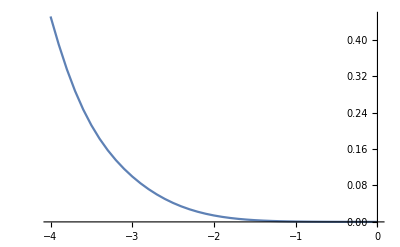

```mathematica
ListLinePlot[Transpose[{epslist,KS}],PlotRange->{Automatic,Full}]
```

```mathematica
Export[NotebookDirectory[]<>"tug_alice_2.csv",{epslist,aliceRange,matrix, KS}]
```

/home/ez/sense/benchmarks/stan_bench/tug/tug_alice_2.csv